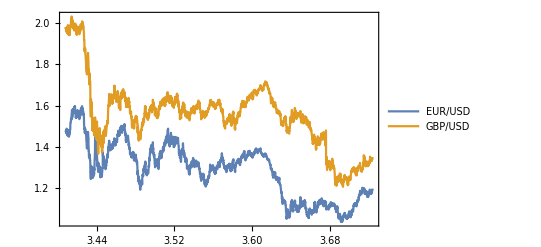

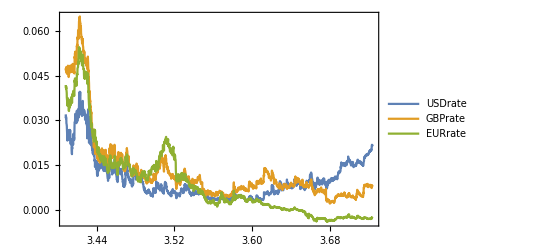

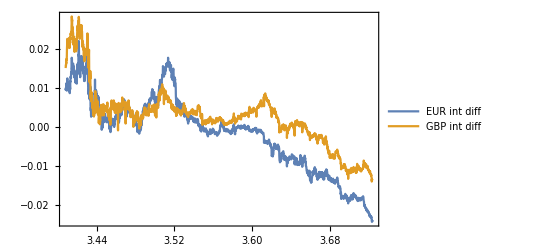

```mathematica
EURUSD=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,5}}];
eurusd=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],5}];
GBPUSD=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,6}}];
gbpusd=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],6}];
USDrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,4}}];
usdrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],4}];
GBPrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,3}}];
gbprate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],3}];
EURrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],{1,2}}];
eurrate=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],2}];
date=Import["/Users/wanghaibiao/Desktop/dk data.xlsx",{"Data",1,Table[i,{i,2,2478}],1}];
gbpdiff=gbprate-usdrate;
eurdiff=eurrate-usdrate;
GBPdiff=Table[{date[[i]],gbpdiff[[i]]},{i,1,2477}];
EURdiff=Table[{date[[i]],eurdiff[[i]]},{i,1,2477}];
DateListPlot[{EURUSD,GBPUSD},PlotLegends->Placed[{"EUR/USD","GBP/USD"},Above]]
DateListPlot[{USDrate,GBPrate,EURrate},PlotRange->All,PlotLegends->Placed[{"USDrate","GBPrate","EURrate"},Above]]
DateListPlot[{EURdiff,GBPdiff},PlotLegends->Placed[{"EUR int diff","GBP int diff"},Above]]
```

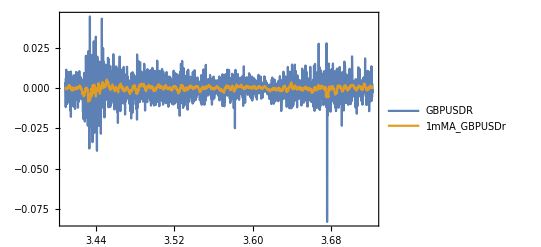

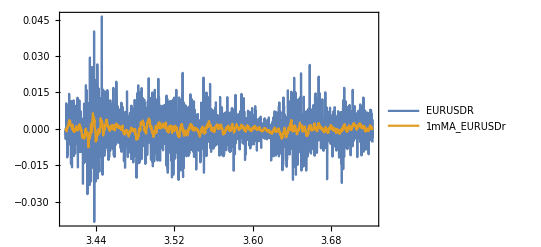

```mathematica
(*Detrended log return*)
gbpusdr=Differences[Log[gbpusd]];
eurusdr=Differences[Log[eurusd]];
GBPUSDr=Table[{date[[i+10]],gbpusdr[[i+10]]},{i,1,2455}];EURUSDr=Table[{date[[i+10]],eurusdr[[i+10]]},{i,1,2455}];
mMAgbpusdr=MovingAverage[gbpusdr,21];
mMAeurusdr=MovingAverage[eurusdr,21];
mMAGBPUSDr=Table[{date[[i+10]],mMAgbpusdr[[i]]},{i,1,2455}];mMAEURUSDr=Table[{date[[i+10]],mMAeurusdr[[i]]},{i,1,2455}];
DateListPlot[{GBPUSDr,mMAGBPUSDr},PlotRange->All,PlotLegends->Placed[{"GBPUSDR","1mMA_GBPUSDr"},Above]]
DateListPlot[{EURUSDr,mMAEURUSDr},PlotRange->All,PlotLegends->Placed[{"EURUSDR","1mMA_EURUSDr"},Above]]
```

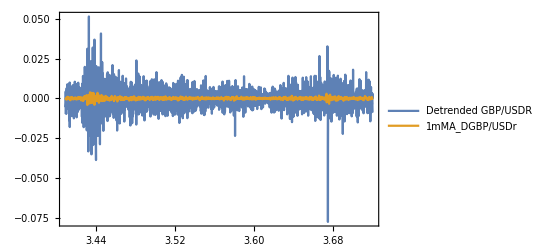

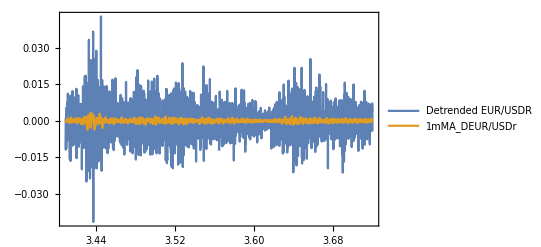

```mathematica
Dgbpusdr= Take[Drop[gbpusdr,10],2456]-mMAgbpusdr;
Deurusdr= Take[Drop[eurusdr,10],2456]-mMAeurusdr;
DGBPUSDr=Table[{date[[i+10]],Dgbpusdr[[i+10]]},{i,1,2435}];
DEURUSDr=Table[{date[[i+10]],Deurusdr[[i+10]]},{i,1,2435}];
mMADgbpusdr=MovingAverage[Dgbpusdr,21];
mMADeurusdr=MovingAverage[Deurusdr,21];
mMADGBPUSDr=Table[{date[[i+10]],mMADgbpusdr[[i]]},{i,1,2435}];mMADEURUSDr=Table[{date[[i+10]],mMADeurusdr[[i]]},{i,1,2435}];
DateListPlot[{DGBPUSDr,mMADGBPUSDr},PlotRange->All,PlotLegends->Placed[{"Detrended GBP/USDR","1mMA_DGBP/USDr"},Above]]
DateListPlot[{DEURUSDr,mMADEURUSDr},PlotRange->All,PlotLegends->Placed[{"Detrended EUR/USDR","1mMA_DEUR/USDr"},Above]]
```

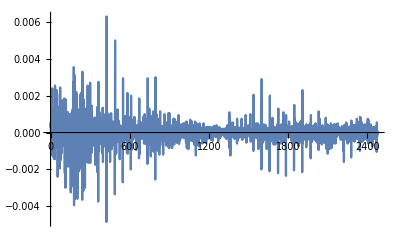

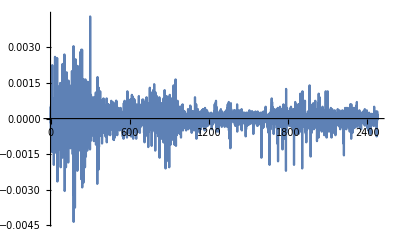

```mathematica
dgbpdiff=Differences[gbpdiff];
deurdiff=Differences[eurdiff];
ListLinePlot[dgbpdiff,PlotRange->All]
ListLinePlot[deurdiff,PlotRange->All]
```

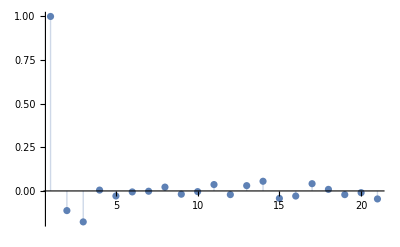

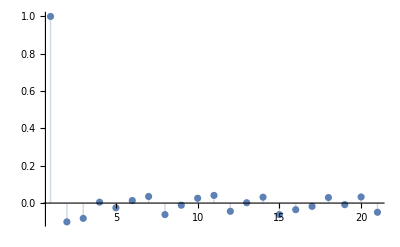

```mathematica
ListPlot[CorrelationFunction[dgbpdiff,{20}],Filling->Axis,PlotRange->All]
ListPlot[CorrelationFunction[deurdiff,{20}],Filling->Axis,PlotRange->All]
```

```mathematica
(*Drift estimation*)
For[n=1,n<18,n++,
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,126*(n-1)+j-1],252];
Subscript[eurusd, n,j]=Take[Drop[eurusd,126*(n-1)+j-1],252];
Subscript[gbpusdr, n,j]=Differences[Log[Subscript[gbpusd, n,j]]];
Subscript[eurusdr, n,j]=Differences[Log[Subscript[eurusd, n,j]]];
Subscript[gbpdiff, n,j]=Take[Drop[gbpdiff,126*(n-1)+j-1],252];
Subscript[eurdiff, n,j]=Take[Drop[eurdiff,126*(n-1)+j-1],252];
Subscript[mMAgbpusdr, n,j]=MovingAverage[Subscript[gbpusdr, n,j],21];
Subscript[mMAeurusdr, n,j]=MovingAverage[Subscript[eurusdr, n,j],21]]]
```

```mathematica
For[n=1,n<18,n++,
For[j=1,j<11,j++,
Subscript[rwgbp, n,j]=TimeSeriesModelFit[Subscript[gbpdiff, n,j],{"ARIMA",{0,1,0}}];
Subscript[rweur, n,j]=TimeSeriesModelFit[Subscript[eurdiff, n,j],{"ARIMA",{0,1,0}}];
Subscript[fgbpdiff, n,j]=TimeSeriesForecast[Subscript[rwgbp, n,j],{10}]["Values"];
Subscript[feurdiff, n,j]=TimeSeriesForecast[Subscript[rweur, n,j],{10}]["Values"];
Subscript[ngbpdiff, n,j]=Join[Subscript[gbpdiff, n,j],Subscript[fgbpdiff, n,j]];
Subscript[neurdiff, n,j]=Join[Subscript[eurdiff, n,j],Subscript[feurdiff, n,j]]]]
```

```mathematica
For[n=1,n<18,n++,
For[j=1,j<11,j++,
For[t=1,t≤242,t++,
Subscript[ngbpdiff, n,j,t]=Take[Drop[Subscript[ngbpdiff, n,j],t-1],21];
Subscript[neurdiff, n,j,t]=Take[Drop[Subscript[neurdiff, n,j],t-1],21];
Subscript[lm1, n,j,t]=LinearModelFit[Subscript[ngbpdiff, n,j,t],x,x];
Subscript[lm2, n,j,t]=LinearModelFit[Subscript[neurdiff, n,j,t],x,x];
Subscript[b1, n,j,t]=Subscript[lm1, n,j,t]["BestFitParameters"][[2]];
Subscript[b2, n,j,t]=Subscript[lm2, n,j,t]["BestFitParameters"][[2]]];
Subscript[b1, n,j]=Table[Subscript[b1, n,j,t],{t,1,242}];
Subscript[b2, n,j]=Table[Subscript[b2, n,j,t],{t,1,242}];
Subscript[empb1, n,j]=EmpiricalDistribution[Subscript[b1, n,j]];
Subscript[empb2, n,j]=EmpiricalDistribution[Subscript[b2, n,j]];
Subscript[empMAr1, n,j]=EmpiricalDistribution[Subscript[mMAgbpusdr, n,j]];
Subscript[empMAr2, n,j]=EmpiricalDistribution[Subscript[mMAeurusdr, n,j]]]]
```

```mathematica
For[n=1,n<18,n++,
For[j=1,j<11,j++,
Subscript[k1, n,j]=x/.Last[Minimize[{Abs[(Quantile[Subscript[empMAr1, n,j],0.975]-Quantile[Subscript[empMAr1, n,j],0.025])-x*(Quantile[Subscript[empb1, n,j],0.975]-Quantile[Subscript[empb1, n,j],0.025])],x>0},x]];
Subscript[k2, n,j]=x/.Last[Minimize[{Abs[(Quantile[Subscript[empMAr2, n,j],0.975]-Quantile[Subscript[empMAr2, n,j],0.025])-x*(Quantile[Subscript[empb2, n,j],0.975]-Quantile[Subscript[empb2, n,j],0.025])],x>0},x]];
Print ["Period=",n,",",j];
Print[Subscript[k1, n,j]];
Print[Subscript[k2, n,j]];
Print[]]]
```

Period=1,1

10.476

11.884

Period=1,2

10.6756

11.884

Period=1,3

10.7845

11.884

Period=1,4

10.7845

11.884

Period=1,5

10.7845

11.884

Period=1,6

10.7845

11.884

Period=1,7

10.7845

11.884

Period=1,8

10.7845

11.884

Period=1,9

10.7845

11.884

Period=1,10

10.7845

11.884

Period=2,1

17.8637

13.487

Period=2,2

18.1422

13.487

Period=2,3

18.1422

13.487

Period=2,4

18.1422

13.487

Period=2,5

18.1422

13.487

Period=2,6

18.1422

13.487

Period=2,7

18.1422

13.487

Period=2,8

18.1422

13.487

Period=2,9

18.1422

13.487

Period=2,10

18.1422

13.487

Period=3,1

17.9695

14.4883

Period=3,2

18.1163

14.4808

Period=3,3

19.0538

14.3147

Period=3,4

19.2644

14.8154

Period=3,5

20.5766

15.524

Period=3,6

20.6507

16.0993

Period=3,7

20.6638

16.1514

Period=3,8

20.8403

16.2257

Period=3,9

21.175

16.298

Period=3,10

21.175

16.2711

Period=4,1

17.3693

16.7673

Period=4,2

17.3693

16.5455

Period=4,3

17.3693

16.3494

Period=4,4

17.3693

16.3712

Period=4,5

17.3693

16.5616

Period=4,6

17.3693

16.7697

Period=4,7

17.0162

16.7697

Period=4,8

16.2547

16.8468

Period=4,9

16.3116

16.908

Period=4,10

16.3085

16.9249

Period=5,1

14.338

18.8811

Period=5,2

14.3636

18.5418

Period=5,3

14.1984

16.9786

Period=5,4

14.6271

17.3296

Period=5,5

15.1317

16.8752

Period=5,6

14.9799

16.4579

Period=5,7

15.5153

15.2138

Period=5,8

15.5692

15.1582

Period=5,9

15.6956

15.3678

Period=5,10

15.8189

15.342

Period=6,1

10.1473

13.7026

Period=6,2

10.1473

13.764

Period=6,3

10.1473

13.488

Period=6,4

10.1473

13.4639

Period=6,5

10.1473

13.3345

Period=6,6

10.1473

13.3243

Period=6,7

10.1473

13.3243

Period=6,8

10.1473

13.3243

Period=6,9

10.1473

12.708

Period=6,10

10.1473

11.4084

Period=7,1

16.7225

9.07794

Period=7,2

16.7225

9.07794

Period=7,3

16.7225

9.07794

Period=7,4

16.7225

9.07794

Period=7,5

17.4566

9.07794

Period=7,6

17.8586

9.07794

Period=7,7

17.8586

9.07794

Period=7,8

17.8586

9.07794

Period=7,9

17.8586

9.07794

Period=7,10

17.8586

9.07794

Period=8,1

15.5727

27.2472

Period=8,2

15.5727

27.9807

Period=8,3

15.5727

28.0714

Period=8,4

15.5727

28.1018

Period=8,5

15.5727

28.4609

Period=8,6

15.5727

29.3834

Period=8,7

15.5727

29.799

Period=8,8

15.5727

29.799

Period=8,9

15.5727

29.799

Period=8,10

15.5727

29.799

Period=9,1

13.9256

21.1898

Period=9,2

13.9256

21.1898

Period=9,3

13.9256

21.1898

Period=9,4

13.9256

21.1898

Period=9,5

13.9256

21.1898

Period=9,6

13.9256

21.1898

Period=9,7

13.9256

21.1898

Period=9,8

13.9256

21.1898

Period=9,9

13.9256

21.1898

Period=9,10

13.9256

21.0597

Period=10,1

29.0965

16.9709

Period=10,2

29.4131

16.9709

Period=10,3

29.4131

16.9709

Period=10,4

29.4131

16.9709

Period=10,5

28.6573

16.9709

Period=10,6

27.6525

16.9709

Period=10,7

26.6464

16.9709

Period=10,8

27.573

16.6783

Period=10,9

27.4342

16.5634

Period=10,10

27.6245

16.2005

Period=11,1

27.7995

22.3038

Period=11,2

27.945

22.2119

Period=11,3

27.7291

21.7528

Period=11,4

27.6489

21.8404

Period=11,5

27.05

21.8992

Period=11,6

27.5391

21.3827

Period=11,7

28.3773

21.0145

Period=11,8

28.3773

20.7779

Period=11,9

28.3773

20.2981

Period=11,10

28.3773

20.1281

Period=12,1

10.8914

13.7116

Period=12,2

11.0077

13.4929

Period=12,3

11.1508

13.1765

Period=12,4

11.153

13.4326

Period=12,5

11.3972

13.4929

Period=12,6

11.5992

13.7116

Period=12,7

12.4428

13.7116

Period=12,8

12.4428

13.7116

Period=12,9

12.1593

13.7116

Period=12,10

11.867

13.7116

Period=13,1

8.73846

10.2991

Period=13,2

8.80492

10.2566

Period=13,3

8.80492

10.2042

Period=13,4

8.80492

10.0448

Period=13,5

8.83689

9.80192

Period=13,6

8.93918

9.77268

Period=13,7

8.9553

9.80192

Period=13,8

8.9553

9.80192

Period=13,9

8.9553

9.80192

Period=13,10

8.9553

9.80192

Period=14,1

15.805

14.0674

Period=14,2

15.805

14.0674

Period=14,3

15.805

14.0674

Period=14,4

15.805

15.294

Period=14,5

15.805

15.294

Period=14,6

15.805

15.294

Period=14,7

15.805

15.294

Period=14,8

15.805

15.294

Period=14,9

15.805

15.294

Period=14,10

15.805

15.294

Period=15,1

24.5029

16.9476

Period=15,2

24.5029

16.8743

Period=15,3

24.5029

16.8743

Period=15,4

24.5029

16.8743

Period=15,5

24.5269

16.8743

Period=15,6

24.5029

16.8743

Period=15,7

24.6958

16.8743

Period=15,8

24.7201

16.8743

Period=15,9

25.2676

16.8743

Period=15,10

25.0983

16.8743

Period=16,1

28.7479

14.8085

Period=16,2

28.7479

14.8085

Period=16,3

28.7479

14.8085

Period=16,4

28.7479

14.8085

Period=16,5

28.7479

14.8085

Period=16,6

28.7479

14.8085

Period=16,7

28.7479

14.8085

Period=16,8

28.7479

14.8085

Period=16,9

28.7479

14.8085

Period=16,10

28.7479

14.8085

Period=17,1

24.9072

14.6355

Period=17,2

24.9072

14.6355

Period=17,3

24.9072

14.6355

Period=17,4

24.845

14.6355

Period=17,5

24.5976

13.9991

Period=17,6

24.5976

13.947

Period=17,7

24.5976

13.4251

Period=17,8

24.5976

13.2025

Period=17,9

24.5976

13.1412

Period=17,10

24.5976

13.0956

```mathematica
For[n=1,n<18,n++,
For[j=1,j<11,j++,
For[t=1,t≤242,t++,
Subscript[msf1, n,j,t]=Subscript[k1, n,j]*Subscript[b1, n,j,t];
Subscript[msf2, n,j,t]=Subscript[k2, n,j]*Subscript[b2, n,j,t]];
Subscript[msf1, n,j]=Table[Subscript[msf1, n,j,t],{t,1,242}];
Subscript[msf2, n,j]=Table[Subscript[msf2, n,j,t],{t,1,242}]]]
```

```mathematica
For[n=1,n<18,n++,
For[j=1,j<11,j++,
Subscript[mgbpusdr, n,j]=Take[Drop[Subscript[gbpusdr, n,j],9],242];
Subscript[meurusdr, n,j]=Take[Drop[Subscript[eurusdr, n,j],9],242];
Subscript[L1, n,j]=(Subscript[mgbpusdr, n,j]+Subscript[msf1, n,j])*100;
Subscript[L2, n,j]=(Subscript[meurusdr, n,j]+Subscript[msf2, n,j])*100]]
```

```mathematica
For[n=1,n<18,n++,
For[j=1,j<11,j++,
Print["Period=",n,",",j];
Print[NSolve[m1+θ1==Mean[Subscript[L1, n,j]]&&σ1^2+θ1^2==Variance[Subscript[L1, n,j]]&&(2*θ1^3+3σ1^2*θ1)/(σ1^2+θ1^2)^1.5==Skewness[Subscript[L1, n,j]]&&σ1>0,{m1,θ1,σ1},Reals]];
Subscript[m1, n,j]=m1/.First[NSolve[m1+θ1==Mean[Subscript[L1, n,j]]&&σ1^2+θ1^2==Variance[Subscript[L1, n,j]]&&(2*θ1^3+3σ1^2*θ1)/(σ1^2+θ1^2)^1.5==Skewness[Subscript[L1, n,j]]&&σ1>0,{m1,θ1,σ1},Reals]];
Subscript[θ1, n,j]=θ1/.First[NSolve[m1+θ1==Mean[Subscript[L1, n,j]]&&σ1^2+θ1^2==Variance[Subscript[L1, n,j]]&&(2*θ1^3+3σ1^2*θ1)/(σ1^2+θ1^2)^1.5==Skewness[Subscript[L1, n,j]]&&σ1>0,{m1,θ1,σ1},Reals]];
Subscript[σ1, n,j]=σ1/.First[NSolve[m1+θ1==Mean[Subscript[L1, n,j]]&&σ1^2+θ1^2==Variance[Subscript[L1, n,j]]&&(2*θ1^3+3σ1^2*θ1)/(σ1^2+θ1^2)^1.5==Skewness[Subscript[L1, n,j]]&&σ1>0,{m1,θ1,σ1},Reals]];
Subscript[m2, n,j]=m2/.First[NSolve[m2+θ2==Mean[Subscript[L2, n,j]]&&σ2^2+θ2^2==Variance[Subscript[L2, n,j]]&&(2*θ2^3+3σ2^2*θ2)/(σ2^2+θ2^2)^1.5==Skewness[Subscript[L2, n,j]]&&σ2>0,{m2,θ2,σ2},Reals]];
Subscript[θ2, n,j]=θ2/.First[NSolve[m2+θ2==Mean[Subscript[L2, n,j]]&&σ2^2+θ2^2==Variance[Subscript[L2, n,j]]&&(2*θ2^3+3σ2^2*θ2)/(σ2^2+θ2^2)^1.5==Skewness[Subscript[L2, n,j]]&&σ2>0,{m2,θ2,σ2},Reals]];
Subscript[σ2, n,j]=σ2/.First[NSolve[m2+θ2==Mean[Subscript[L2, n,j]]&&σ2^2+θ2^2==Variance[Subscript[L2, n,j]]&&(2*θ2^3+3σ2^2*θ2)/(σ2^2+θ2^2)^1.5==Skewness[Subscript[L2, n,j]]&&σ2>0,{m2,θ2,σ2},Reals]];Print[NSolve[m2+θ2==Mean[Subscript[L2, n,j]]&&σ2^2+θ2^2==Variance[Subscript[L2, n,j]]&&(2*θ2^3+3σ2^2*θ2)/(σ2^2+θ2^2)^1.5==Skewness[Subscript[L2, n,j]]&&σ2>0,{m2,θ2,σ2},Reals]]]]
```

Period=1,1

{{θ1→-0.0955918,σ1→1.00388,m1→-0.0780959}}

{{θ2→-0.0369308,σ2→0.994523,m2→-0.0173127}}

Period=1,2

{{θ1→-0.0593108,σ1→1.0297,m1→-0.103246}}

{{θ2→-0.0373843,σ2→1.00153,m2→-0.00523067}}

Period=1,3

{{θ1→-0.0606831,σ1→1.02662,m1→-0.108102}}

{{θ2→-0.0413458,σ2→1.00256,m2→-0.00172516}}

Period=1,4

{{θ1→-0.0636874,σ1→1.02618,m1→-0.100626}}

{{θ2→-0.0391607,σ2→1.00687,m2→-0.00761479}}

Period=1,5

{{θ1→-0.0697177,σ1→1.03655,m1→-0.108913}}

{{θ2→-0.0357764,σ2→1.00945,m2→-0.0155072}}

Period=1,6

{{θ1→-0.0666657,σ1→1.04347,m1→-0.117226}}

{{θ2→-0.0350039,σ2→1.01315,m2→-0.020948}}

Period=1,7

{{θ1→-0.0661586,σ1→1.03846,m1→-0.123588}}

{{θ2→-0.0320755,σ2→1.01043,m2→-0.0283562}}

Period=1,8

{{θ1→-0.0666737,σ1→1.03647,m1→-0.127701}}

{{θ2→-0.0306152,σ2→1.01226,m2→-0.0337986}}

Period=1,9

{{θ1→-0.0589939,σ1→1.04477,m1→-0.12754}}

{{θ2→-0.0302806,σ2→1.01609,m2→-0.0316484}}

Period=1,10

{{θ1→-0.0591544,σ1→1.05207,m1→-0.137751}}

{{θ2→-0.027332,σ2→1.01645,m2→-0.0347556}}

Period=2,1

{{θ1→-0.0525866,σ1→1.27147,m1→-0.154584}}

{{θ2→0.144579,σ2→1.11706,m2→-0.277175}}

Period=2,2

{{θ1→-0.0539587,σ1→1.27254,m1→-0.155791}}

{{θ2→0.144961,σ2→1.117,m2→-0.277981}}

Period=2,3

{{θ1→-0.0515287,σ1→1.27291,m1→-0.161293}}

{{θ2→0.142913,σ2→1.11721,m2→-0.273877}}

Period=2,4

{{θ1→-0.0568853,σ1→1.27427,m1→-0.149218}}

{{θ2→0.140023,σ2→1.1157,m2→-0.26663}}

Period=2,5

{{θ1→-0.0635264,σ1→1.2735,m1→-0.134365}}

{{θ2→0.136713,σ2→1.11798,m2→-0.259499}}

Period=2,6

{{θ1→-0.064273,σ1→1.27345,m1→-0.132869}}

{{θ2→0.134917,σ2→1.11833,m2→-0.255866}}

Period=2,7

{{θ1→-0.0614526,σ1→1.27416,m1→-0.138928}}

{{θ2→0.136602,σ2→1.11786,m2→-0.25934}}

Period=2,8

{{θ1→-0.0695423,σ1→1.27499,m1→-0.120496}}

{{θ2→0.128977,σ2→1.11829,m2→-0.241684}}

Period=2,9

{{θ1→-0.0728565,σ1→1.27549,m1→-0.112793}}

{{θ2→0.125382,σ2→1.11895,m2→-0.234129}}

Period=2,10

{{θ1→-0.0741101,σ1→1.27573,m1→-0.109908}}

{{θ2→0.126494,σ2→1.11866,m2→-0.236415}}

Period=3,1

{{θ1→0.0958411,σ1→0.892998,m1→-0.0307751}}

{{θ2→0.215303,σ2→0.767965,m2→-0.181399}}

Period=3,2

{{θ1→0.105937,σ1→0.881568,m1→-0.0321318}}

{{θ2→0.215161,σ2→0.768099,m2→-0.180846}}

Period=3,3

{{θ1→0.104334,σ1→0.879946,m1→-0.0255728}}

{{θ2→0.226715,σ2→0.755868,m2→-0.188242}}

Period=3,4

{{θ1→0.103422,σ1→0.875801,m1→-0.0263449}}

{{θ2→0.216476,σ2→0.746979,m2→-0.187777}}

Period=3,5

{{θ1→0.108415,σ1→0.873778,m1→-0.0362396}}

{{θ2→0.214924,σ2→0.751378,m2→-0.188924}}

Period=3,6

{{θ1→0.103847,σ1→0.877049,m1→-0.0243072}}

{{θ2→0.214266,σ2→0.754526,m2→-0.190375}}

Period=3,7

{{θ1→0.104745,σ1→0.876719,m1→-0.026674}}

{{θ2→0.218318,σ2→0.751352,m2→-0.19381}}

Period=3,8

{{θ1→0.108792,σ1→0.876481,m1→-0.0357995}}

{{θ2→0.258979,σ2→0.721235,m2→-0.225332}}

Period=3,9

{{θ1→0.125013,σ1→0.86318,m1→-0.0461181}}

{{θ2→0.254928,σ2→0.72272,m2→-0.216995}}

Period=3,10

{{θ1→0.126588,σ1→0.861072,m1→-0.0506061}}

{{θ2→0.257872,σ2→0.719714,m2→-0.222445}}

Period=4,1

{{θ1→0.00650677,σ1→0.736934,m1→-0.0546515}}

{{θ2→0.0210242,σ2→0.705691,m2→-0.0414739}}

Period=4,2

{{θ1→0.0044673,σ1→0.73617,m1→-0.0493272}}

{{θ2→0.0185064,σ2→0.706931,m2→-0.0335763}}

Period=4,3

{{θ1→0.00837219,σ1→0.736669,m1→-0.0585146}}

{{θ2→0.0181497,σ2→0.707359,m2→-0.0315597}}

Period=4,4

{{θ1→0.00525104,σ1→0.737746,m1→-0.0505666}}

{{θ2→0.0184607,σ2→0.707457,m2→-0.0327894}}

Period=4,5

{{θ1→0.00403608,σ1→0.736989,m1→-0.048398}}

{{θ2→0.0177779,σ2→0.705823,m2→-0.0320501}}

Period=4,6

{{θ1→0.00409387,σ1→0.736959,m1→-0.0486667}}

{{θ2→0.015913,σ2→0.708244,m2→-0.0274416}}

Period=4,7

{{θ1→0.00372775,σ1→0.740379,m1→-0.0420259}}

{{θ2→0.0196183,σ2→0.707157,m2→-0.0369457}}

Period=4,8

{{θ1→-0.0091922,σ1→0.729804,m1→-0.0322229}}

{{θ2→0.0105763,σ2→0.702901,m2→-0.0278405}}

Period=4,9

{{θ1→-0.012293,σ1→0.731173,m1→-0.0250625}}

{{θ2→0.00873961,σ2→0.704327,m2→-0.0230791}}

Period=4,10

{{θ1→-0.013278,σ1→0.732068,m1→-0.0224857}}

{{θ2→0.00773231,σ2→0.705429,m2→-0.019714}}

Period=5,1

{{θ1→-0.00150522,σ1→0.690798,m1→0.0156251}}

{{θ2→0.0404543,σ2→0.80963,m2→-0.0213629}}

Period=5,2

{{θ1→0.000775085,σ1→0.69234,m1→0.0100045}}

{{θ2→0.0411254,σ2→0.808444,m2→-0.0223666}}

Period=5,3

{{θ1→-0.00173498,σ1→0.694318,m1→0.0191847}}

{{θ2→0.0428416,σ2→0.808636,m2→-0.0159026}}

Period=5,4

{{θ1→-0.00458869,σ1→0.691926,m1→0.0257967}}

{{θ2→0.0384321,σ2→0.812041,m2→-0.0049698}}

Period=5,5

{{θ1→-0.00758157,σ1→0.693174,m1→0.0242711}}

{{θ2→0.0372741,σ2→0.810531,m2→-0.00264815}}

Period=5,6

{{θ1→-0.00709566,σ1→0.693389,m1→0.0273241}}

{{θ2→0.0371774,σ2→0.809129,m2→-0.00253635}}

Period=5,7

{{θ1→-0.0102341,σ1→0.695159,m1→0.0367987}}

{{θ2→0.0352043,σ2→0.806451,m2→0.00358198}}

Period=5,8

{{θ1→-0.0080068,σ1→0.691691,m1→0.0362318}}

{{θ2→0.0359526,σ2→0.803879,m2→0.00549969}}

Period=5,9

{{θ1→-0.00951161,σ1→0.691332,m1→0.0482078}}

{{θ2→0.0319701,σ2→0.803636,m2→0.0167124}}

Period=5,10

{{θ1→-0.0119109,σ1→0.694456,m1→0.058238}}

{{θ2→0.0296795,σ2→0.805041,m2→0.0220063}}

Period=6,1

{{θ1→0.0313262,σ1→0.590638,m1→-0.0137979}}

{{θ2→-0.0421378,σ2→0.77436,m2→0.117293}}

Period=6,2

{{θ1→0.0307527,σ1→0.591805,m1→-0.0116877}}

{{θ2→-0.0453496,σ2→0.776933,m2→0.127836}}

Period=6,3

{{θ1→0.0263594,σ1→0.584376,m1→-0.0160429}}

{{θ2→-0.0420249,σ2→0.773352,m2→0.112922}}

Period=6,4

{{θ1→0.0277975,σ1→0.584068,m1→-0.0188217}}

{{θ2→-0.0392099,σ2→0.77446,m2→0.106638}}

Period=6,5

{{θ1→0.0245956,σ1→0.584033,m1→-0.0111426}}

{{θ2→-0.043097,σ2→0.772872,m2→0.114414}}

Period=6,6

{{θ1→0.0233312,σ1→0.586965,m1→-0.0125303}}

{{θ2→-0.0425914,σ2→0.777519,m2→0.108525}}

Period=6,7

{{θ1→0.0240226,σ1→0.584877,m1→-0.0156911}}

{{θ2→-0.040802,σ2→0.775884,m2→0.100742}}

Period=6,8

{{θ1→0.0215381,σ1→0.586287,m1→-0.00981191}}

{{θ2→-0.0438775,σ2→0.775523,m2→0.10647}}

Period=6,9

{{θ1→0.0315258,σ1→0.578888,m1→-0.0157993}}

{{θ2→-0.0437657,σ2→0.77385,m2→0.100854}}

Period=6,10

{{θ1→0.0290637,σ1→0.578147,m1→-0.0110059}}

{{θ2→-0.0425525,σ2→0.76247,m2→0.100995}}

Period=7,1

{{θ1→0.00631151,σ1→0.607652,m1→-0.0546581}}

{{θ2→-0.0750726,σ2→0.763543,m2→0.0223757}}

Period=7,2

{{θ1→0.00570293,σ1→0.608149,m1→-0.0529548}}

{{θ2→-0.0755741,σ2→0.75944,m2→0.0280793}}

Period=7,3

{{θ1→0.00404191,σ1→0.607662,m1→-0.0495861}}

{{θ2→-0.0771655,σ2→0.758394,m2→0.0310747}}

Period=7,4

{{θ1→0.00385698,σ1→0.608383,m1→-0.0485093}}

{{θ2→-0.0767213,σ2→0.758215,m2→0.029606}}

Period=7,5

{{θ1→0.00266987,σ1→0.611203,m1→-0.0459512}}

{{θ2→-0.0772602,σ2→0.757306,m2→0.0294909}}

Period=7,6

{{θ1→0.00464876,σ1→0.611786,m1→-0.0504314}}

{{θ2→-0.0754368,σ2→0.757496,m2→0.0262682}}

Period=7,7

{{θ1→0.00446269,σ1→0.612126,m1→-0.0496755}}

{{θ2→-0.0764586,σ2→0.756343,m2→0.0289021}}

Period=7,8

{{θ1→0.00343872,σ1→0.611523,m1→-0.0478945}}

{{θ2→-0.076065,σ2→0.756326,m2→0.0276629}}

Period=7,9

{{θ1→0.0028329,σ1→0.612108,m1→-0.0465001}}

{{θ2→-0.0777692,σ2→0.759625,m2→0.0365973}}

Period=7,10

{{θ1→0.00314903,σ1→0.607119,m1→-0.0540857}}

{{θ2→-0.0766436,σ2→0.759112,m2→0.0343316}}

Period=8,1

{{θ1→0.0176281,σ1→0.593467,m1→-0.0555078}}

{{θ2→0.00861124,σ2→0.725911,m2→-0.169243}}

Period=8,2

{{θ1→0.0174359,σ1→0.593044,m1→-0.0538659}}

{{θ2→0.00754509,σ2→0.729135,m2→-0.17375}}

Period=8,3

{{θ1→0.0142825,σ1→0.593927,m1→-0.0455543}}

{{θ2→0.0102543,σ2→0.733643,m2→-0.164031}}

Period=8,4

{{θ1→0.0155105,σ1→0.592772,m1→-0.0494838}}

{{θ2→0.00722674,σ2→0.734322,m2→-0.159635}}

Period=8,5

{{θ1→0.0158539,σ1→0.59246,m1→-0.0501934}}

{{θ2→0.00562545,σ2→0.73276,m2→-0.154186}}

Period=8,6

{{θ1→0.015826,σ1→0.589922,m1→-0.0521869}}

{{θ2→0.00690597,σ2→0.729932,m2→-0.168038}}

Period=8,7

{{θ1→0.0168149,σ1→0.589816,m1→-0.0540279}}

{{θ2→0.00605341,σ2→0.729898,m2→-0.169968}}

Period=8,8

{{θ1→0.0158476,σ1→0.587023,m1→-0.0555173}}

{{θ2→0.00706037,σ2→0.729749,m2→-0.172254}}

Period=8,9

{{θ1→0.0130996,σ1→0.586445,m1→-0.049169}}

{{θ2→0.00435889,σ2→0.726958,m2→-0.162328}}

Period=8,10

{{θ1→0.014586,σ1→0.584395,m1→-0.0537798}}

{{θ2→0.00688952,σ2→0.725899,m2→-0.167414}}

Period=9,1

{{θ1→-0.0119012,σ1→0.453134,m1→-0.00303995}}

{{θ2→0.0359561,σ2→0.601493,m2→-0.0410071}}

Period=9,2

{{θ1→-0.0116852,σ1→0.452641,m1→-0.00315799}}

{{θ2→0.0366664,σ2→0.599046,m2→-0.0374771}}

Period=9,3

{{θ1→-0.0103357,σ1→0.452403,m1→-0.00582934}}

{{θ2→0.0370204,σ2→0.598893,m2→-0.0383842}}

Period=9,4

{{θ1→-0.0115741,σ1→0.449935,m1→0.000357241}}

{{θ2→0.0336868,σ2→0.601762,m2→-0.0387051}}

Period=9,5

{{θ1→-0.0102146,σ1→0.453192,m1→0.00132738}}

{{θ2→0.0326489,σ2→0.60094,m2→-0.0367313}}

Period=9,6

{{θ1→-0.0141357,σ1→0.458549,m1→-0.00122497}}

{{θ2→0.0321516,σ2→0.600618,m2→-0.0352716}}

Period=9,7

{{θ1→-0.0124328,σ1→0.457747,m1→-0.00423037}}

{{θ2→0.0319529,σ2→0.599203,m2→-0.0362494}}

Period=9,8

{{θ1→-0.0115641,σ1→0.460137,m1→-0.00787934}}

{{θ2→0.0348557,σ2→0.598034,m2→-0.043219}}

Period=9,9

{{θ1→-0.00908624,σ1→0.455856,m1→-0.00642565}}

{{θ2→0.0346201,σ2→0.600781,m2→-0.0467722}}

Period=9,10

{{θ1→-0.0082946,σ1→0.455676,m1→-0.00804861}}

{{θ2→0.0363394,σ2→0.599963,m2→-0.0505211}}

Period=10,1

{{θ1→-0.128317,σ1→0.488262,m1→0.128837}}

{{θ2→-0.000761614,σ2→0.540919,m2→0.0458797}}

Period=10,2

{{θ1→-0.129028,σ1→0.488268,m1→0.129169}}

{{θ2→-0.000699922,σ2→0.540639,m2→0.0454908}}

Period=10,3

{{θ1→-0.130574,σ1→0.487043,m1→0.132256}}

{{θ2→-0.00107645,σ2→0.539551,m2→0.0471791}}

Period=10,4

{{θ1→-0.128236,σ1→0.488551,m1→0.129642}}

{{θ2→0.00144153,σ2→0.540059,m2→0.0415666}}

Period=10,5

{{θ1→-0.126378,σ1→0.487677,m1→0.126888}}

{{θ2→0.000458883,σ2→0.536201,m2→0.037541}}

Period=10,6

{{θ1→-0.125715,σ1→0.488541,m1→0.129117}}

{{θ2→-0.000586224,σ2→0.536349,m2→0.0394047}}

Period=10,7

{{θ1→-0.124802,σ1→0.487179,m1→0.127936}}

{{θ2→-0.000721421,σ2→0.532947,m2→0.0360001}}

Period=10,8

{{θ1→-0.128462,σ1→0.486905,m1→0.134545}}

{{θ2→-0.00323836,σ2→0.532808,m2→0.0423094}}

Period=10,9

{{θ1→-0.128842,σ1→0.487783,m1→0.136844}}

{{θ2→-0.00237491,σ2→0.53192,m2→0.0400981}}

Period=10,10

{{θ1→-0.129106,σ1→0.486724,m1→0.135232}}

{{θ2→-0.00465454,σ2→0.53197,m2→0.045111}}

Period=11,1

{{θ1→-0.124333,σ1→0.485674,m1→0.178459}}

{{θ2→-0.0436864,σ2→0.488695,m2→0.0465859}}

Period=11,2

{{θ1→-0.124491,σ1→0.481016,m1→0.1852}}

{{θ2→-0.0445677,σ2→0.488451,m2→0.0480179}}

Period=11,3

{{θ1→-0.129079,σ1→0.4803,m1→0.200343}}

{{θ2→-0.035934,σ2→0.48255,m2→0.0427737}}

Period=11,4

{{θ1→-0.130787,σ1→0.48025,m1→0.203981}}

{{θ2→-0.038281,σ2→0.482138,m2→0.0499311}}

Period=11,5

{{θ1→-0.126958,σ1→0.476452,m1→0.208628}}

{{θ2→-0.0382931,σ2→0.482303,m2→0.0502651}}

Period=11,6

{{θ1→-0.127855,σ1→0.474668,m1→0.206926}}

{{θ2→-0.0341308,σ2→0.476428,m2→0.0537876}}

Period=11,7

{{θ1→-0.129382,σ1→0.474027,m1→0.208726}}

{{θ2→-0.0335622,σ2→0.475572,m2→0.0519871}}

Period=11,8

{{θ1→-0.127717,σ1→0.475521,m1→0.206483}}

{{θ2→-0.0337484,σ2→0.474988,m2→0.052591}}

Period=11,9

{{θ1→-0.124158,σ1→0.469174,m1→0.209592}}

{{θ2→-0.0349853,σ2→0.471517,m2→0.0587123}}

Period=11,10

{{θ1→-0.121476,σ1→0.47001,m1→0.20371}}

{{θ2→-0.034034,σ2→0.471466,m2→0.0568136}}

Period=12,1

{{θ1→0.0207917,σ1→0.355661,m1→0.0217925}}

{{θ2→0.017046,σ2→0.3655,m2→-0.0374425}}

Period=12,2

{{θ1→0.0236962,σ1→0.352356,m1→0.0215127}}

{{θ2→0.0158518,σ2→0.365097,m2→-0.0344245}}

Period=12,3

{{θ1→0.0244639,σ1→0.352536,m1→0.0201744}}

{{θ2→0.0164145,σ2→0.363865,m2→-0.0355759}}

Period=12,4

{{θ1→0.0230101,σ1→0.351551,m1→0.0243628}}

{{θ2→0.0168449,σ2→0.3641,m2→-0.036964}}

Period=12,5

{{θ1→0.0212257,σ1→0.355485,m1→0.0229979}}

{{θ2→0.0170808,σ2→0.363607,m2→-0.0370133}}

Period=12,6

{{θ1→0.0200783,σ1→0.355036,m1→0.0265448}}

{{θ2→0.022288,σ2→0.359612,m2→-0.0407939}}

Period=12,7

{{θ1→0.0203773,σ1→0.35701,m1→0.0264425}}

{{θ2→0.0216275,σ2→0.359067,m2→-0.0390703}}

Period=12,8

{{θ1→0.0221203,σ1→0.35691,m1→0.0218267}}

{{θ2→0.0219522,σ2→0.360015,m2→-0.040802}}

Period=12,9

{{θ1→0.022433,σ1→0.354847,m1→0.0177905}}

{{θ2→0.0242986,σ2→0.360363,m2→-0.0466486}}

Period=12,10

{{θ1→0.0216856,σ1→0.3543,m1→0.0186092}}

{{θ2→0.024559,σ2→0.358174,m2→-0.0444902}}

Period=13,1

{{θ1→-0.0394466,σ1→0.368889,m1→-0.0133927}}

{{θ2→-0.0592838,σ2→0.432889,m2→-0.0506669}}

Period=13,2

{{θ1→-0.0379918,σ1→0.373009,m1→-0.00886629}}

{{θ2→-0.0599295,σ2→0.432583,m2→-0.0481815}}

Period=13,3

{{θ1→-0.0375136,σ1→0.372464,m1→-0.010872}}

{{θ2→-0.0601077,σ2→0.432714,m2→-0.0476006}}

Period=13,4

{{θ1→-0.0361744,σ1→0.371495,m1→-0.0169277}}

{{θ2→-0.0661915,σ2→0.426088,m2→-0.0457022}}

Period=13,5

{{θ1→-0.0373804,σ1→0.372777,m1→-0.0122078}}

{{θ2→-0.067193,σ2→0.425424,m2→-0.0432581}}

Period=13,6

{{θ1→-0.0382739,σ1→0.373145,m1→-0.00883119}}

{{θ2→-0.0682193,σ2→0.425358,m2→-0.0407286}}

Period=13,7

{{θ1→-0.0382852,σ1→0.372725,m1→-0.00951634}}

{{θ2→-0.068632,σ2→0.425753,m2→-0.0396871}}

Period=13,8

{{θ1→-0.0374457,σ1→0.373707,m1→-0.0121}}

{{θ2→-0.0750808,σ2→0.427485,m2→-0.0422963}}

Period=13,9

{{θ1→-0.0379611,σ1→0.374513,m1→-0.0095738}}

{{θ2→-0.0746634,σ2→0.427228,m2→-0.0427484}}

Period=13,10

{{θ1→-0.0380639,σ1→0.374421,m1→-0.0100655}}

{{θ2→-0.0735494,σ2→0.427367,m2→-0.0455649}}

Period=14,1

{{θ1→0.00114112,σ1→0.519418,m1→-0.054982}}

{{θ2→0.0137439,σ2→0.68502,m2→-0.113376}}

Period=14,2

{{θ1→0.00167184,σ1→0.519182,m1→-0.0565261}}

{{θ2→0.0155042,σ2→0.690823,m2→-0.109235}}

Period=14,3

{{θ1→-0.000263541,σ1→0.517275,m1→-0.0504173}}

{{θ2→0.0142738,σ2→0.6956,m2→-0.0994037}}

Period=14,4

{{θ1→-0.00447452,σ1→0.518222,m1→-0.0399317}}

{{θ2→0.0513071,σ2→0.718528,m2→-0.1243}}

Period=14,5

{{θ1→-0.00448584,σ1→0.516997,m1→-0.0398472}}

{{θ2→0.051326,σ2→0.714456,m2→-0.124705}}

Period=14,6

{{θ1→-0.00641006,σ1→0.519033,m1→-0.0380549}}

{{θ2→0.0520924,σ2→0.715383,m2→-0.122322}}

Period=14,7

{{θ1→-0.0051093,σ1→0.518168,m1→-0.0390154}}

{{θ2→0.0464742,σ2→0.721668,m2→-0.122164}}

Period=14,8

{{θ1→-0.00646481,σ1→0.518045,m1→-0.0381154}}

{{θ2→0.0401156,σ2→0.720751,m2→-0.11492}}

Period=14,9

{{θ1→-0.00496501,σ1→0.517167,m1→-0.0386348}}

{{θ2→0.0396491,σ2→0.721761,m2→-0.110554}}

Period=14,10

{{θ1→-0.00295138,σ1→0.51644,m1→-0.0439977}}

{{θ2→0.0401798,σ2→0.721787,m2→-0.111507}}

Period=15,1

{{θ1→0.0474726,σ1→0.588198,m1→-0.101765}}

{{θ2→0.0511461,σ2→0.776765,m2→-0.0791678}}

Period=15,2

{{θ1→0.0433093,σ1→0.59231,m1→-0.100908}}

{{θ2→0.0499595,σ2→0.773111,m2→-0.0724073}}

Period=15,3

{{θ1→0.0418233,σ1→0.591597,m1→-0.0967889}}

{{θ2→0.0477697,σ2→0.772576,m2→-0.0674673}}

Period=15,4

{{θ1→0.0464002,σ1→0.588766,m1→-0.101558}}

{{θ2→0.0558275,σ2→0.768681,m2→-0.0764677}}

Period=15,5

{{θ1→0.0439485,σ1→0.590857,m1→-0.0993228}}

{{θ2→0.0572292,σ2→0.770576,m2→-0.0811998}}

Period=15,6

{{θ1→0.0423695,σ1→0.592151,m1→-0.0990581}}

{{θ2→0.059804,σ2→0.765579,m2→-0.0795432}}

Period=15,7

{{θ1→0.0440921,σ1→0.589,m1→-0.0908914}}

{{θ2→0.06246,σ2→0.760813,m2→-0.0783168}}

Period=15,8

{{θ1→0.0415559,σ1→0.588957,m1→-0.0825071}}

{{θ2→0.0611682,σ2→0.76261,m2→-0.0748629}}

Period=15,9

{{θ1→0.0434394,σ1→0.58466,m1→-0.0798029}}

{{θ2→0.0576611,σ2→0.761252,m2→-0.0651935}}

Period=15,10

{{θ1→0.0443654,σ1→0.58449,m1→-0.0833858}}

{{θ2→0.0608452,σ2→0.761132,m2→-0.0724229}}

Period=16,1

{}

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::nofirst: {} has zero length and no first element.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

ReplaceAll::reps: {First[{}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{θ2→0.0695895,σ2→0.628985,m2→-0.0958911}}

Period=16,2

{}

{{θ2→0.0692892,σ2→0.629207,m2→-0.0954849}}

Period=16,3

{}

{{θ2→0.0727317,σ2→0.62806,m2→-0.103048}}

Period=16,4

{}

{{θ2→0.0691578,σ2→0.632839,m2→-0.10237}}

Period=16,5

{}

{{θ2→0.0712968,σ2→0.632352,m2→-0.106802}}

Period=16,6

{}

{{θ2→0.0711439,σ2→0.6323,m2→-0.106157}}

Period=16,7

{}

{{θ2→0.0720598,σ2→0.632479,m2→-0.108158}}

Period=16,8

{}

{{θ2→0.0690205,σ2→0.634173,m2→-0.100452}}

Period=16,9

{}

{{θ2→0.0695541,σ2→0.634072,m2→-0.101698}}

Period=16,10

{}

{{θ2→0.0688546,σ2→0.634429,m2→-0.100784}}

Period=17,1

{}

{{θ2→-0.0183529,σ2→0.584049,m2→-0.0324904}}

Period=17,2

{}

{{θ2→-0.0178682,σ2→0.58483,m2→-0.0350291}}

Period=17,3

{}

{{θ2→-0.0192961,σ2→0.579895,m2→-0.0407385}}

Period=17,4

{}

{{θ2→-0.0208698,σ2→0.579856,m2→-0.0361748}}

Period=17,5

{}

{{θ2→-0.0239264,σ2→0.578328,m2→-0.0274985}}

Period=17,6

{}

{{θ2→-0.0225861,σ2→0.578295,m2→-0.0302422}}

Period=17,7

{}

{{θ2→-0.0224137,σ2→0.577292,m2→-0.029377}}

Period=17,8

{}

{{θ2→-0.0653133,σ2→0.55527,m2→0.00491853}}

Period=17,9

{}

{{θ2→-0.0670467,σ2→0.556947,m2→0.0110014}}

Period=17,10

{}

{{θ2→-0.0679712,σ2→0.556613,m2→0.0126225}}

```mathematica
For[n=1,n<16,n++,
For[j=1,j<11,j++,
Subscript[F1, n,j]=Function[x,((2*Exp[Subscript[θ1, n,j]*(x-Subscript[m1, n,j])/Subscript[σ1, n,j]^2])/(Subscript[σ1, n,j]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m1, n,j])^2/(2*Subscript[σ1, n,j]^2+Subscript[θ1, n,j]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m1, n,j])^2*(2*Subscript[σ1, n,j]^2+Subscript[θ1, n,j]^2)]/Subscript[σ1, n,j]^2]][x]]]
```

Period=1,1

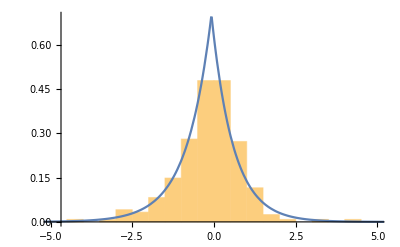

Period=1,2

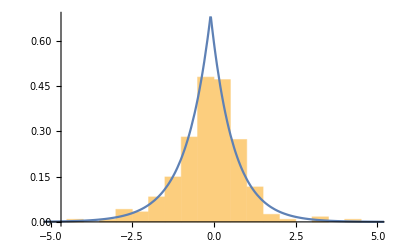

Period=1,3

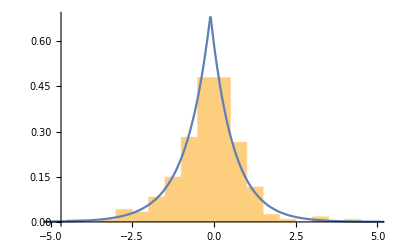

Period=1,4

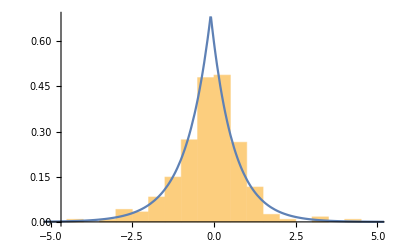

Period=1,5

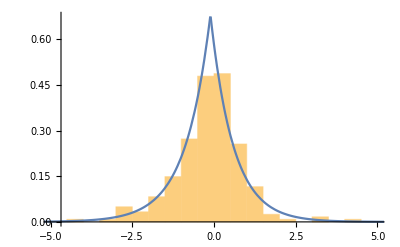

Period=1,6

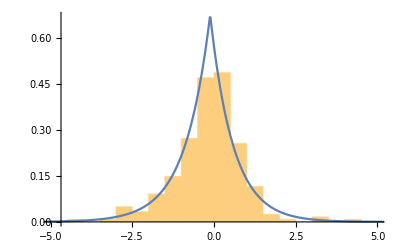

Period=1,7

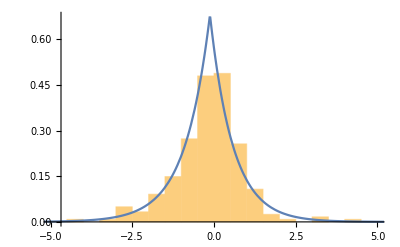

Period=1,8

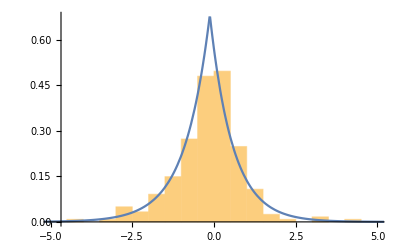

Period=1,9

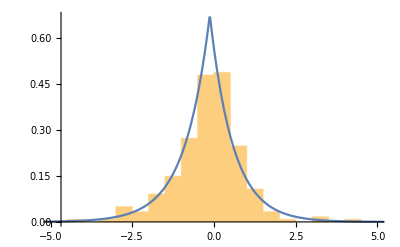

Period=1,10

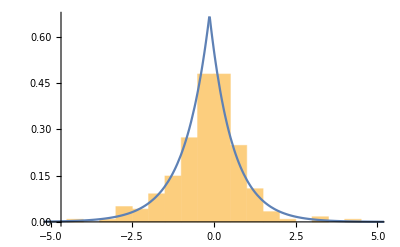

Period=2,1

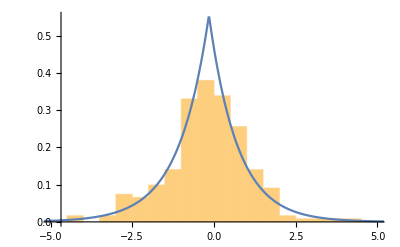

Period=2,2

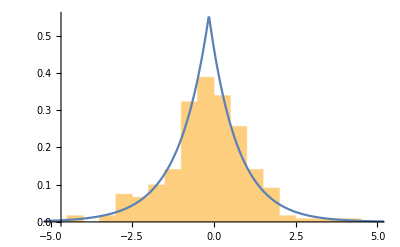

Period=2,3

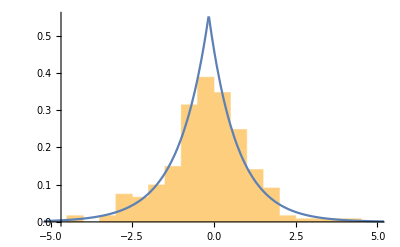

Period=2,4

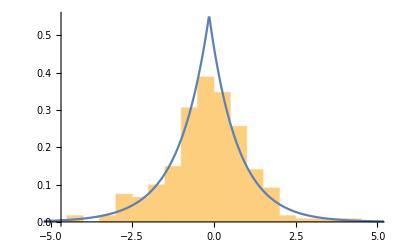

Period=2,5

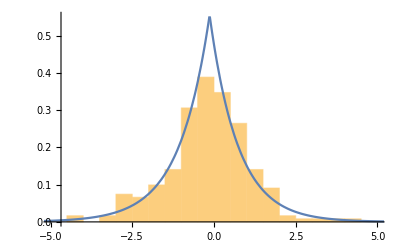

Period=2,6

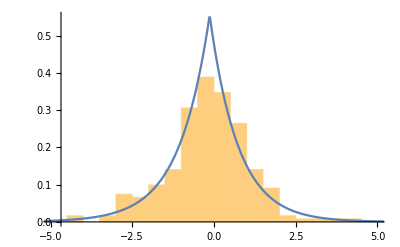

Period=2,7

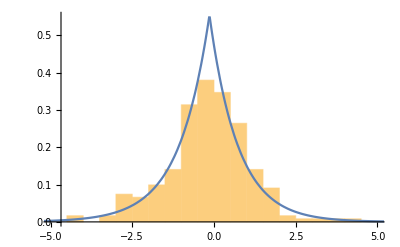

Period=2,8

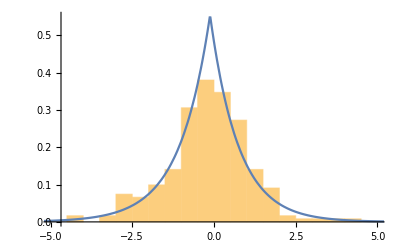

Period=2,9

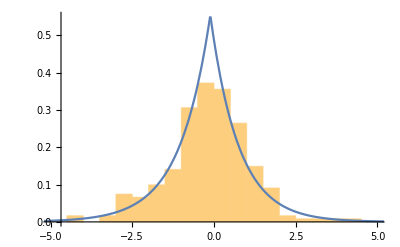

Period=2,10

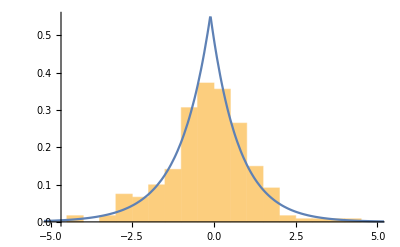

Period=3,1

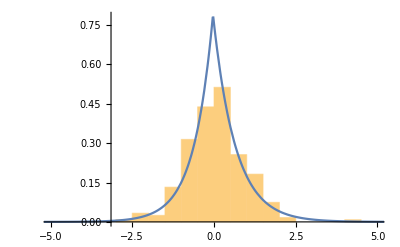

Period=3,2

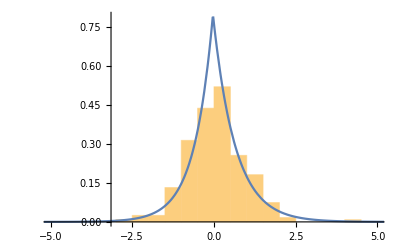

Period=3,3

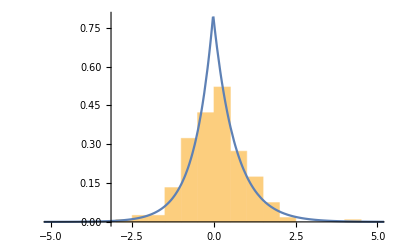

Period=3,4

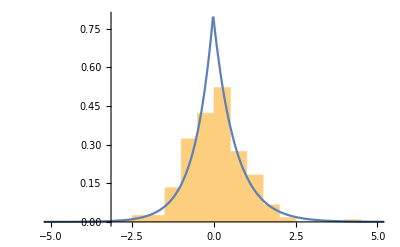

Period=3,5

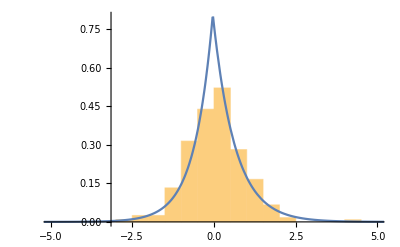

Period=3,6

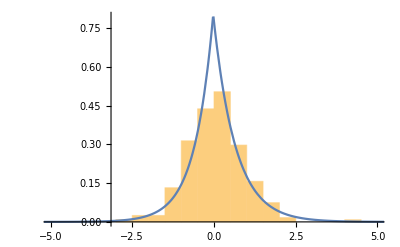

Period=3,7

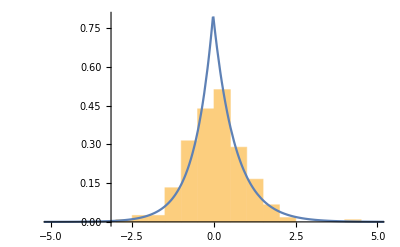

Period=3,8

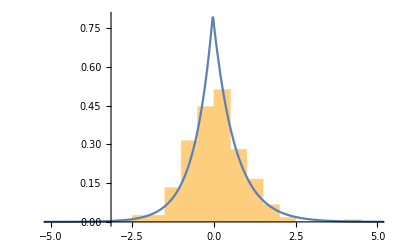

Period=3,9

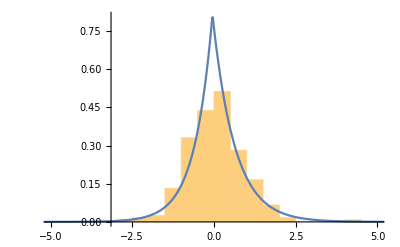

Period=3,10

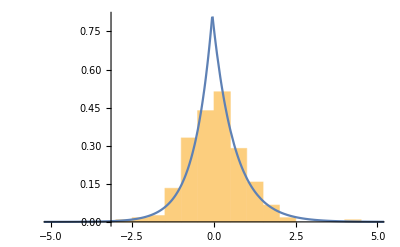

Period=4,1

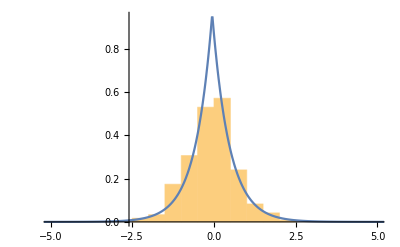

Period=4,2

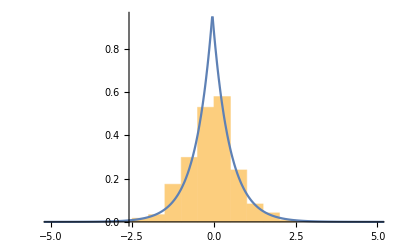

Period=4,3

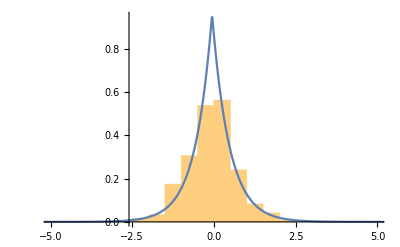

Period=4,4

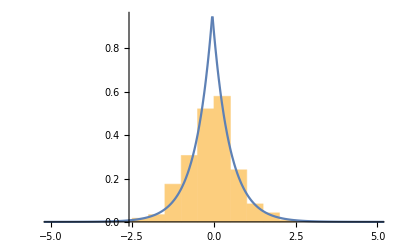

Period=4,5

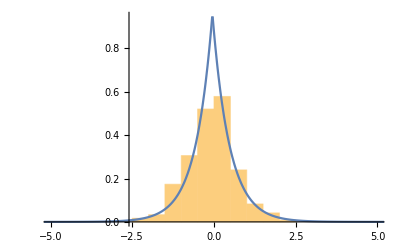

Period=4,6

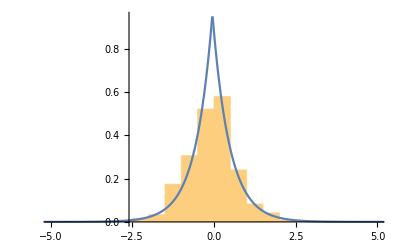

Period=4,7

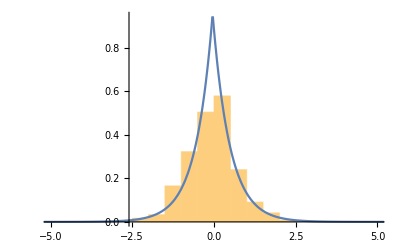

Period=4,8

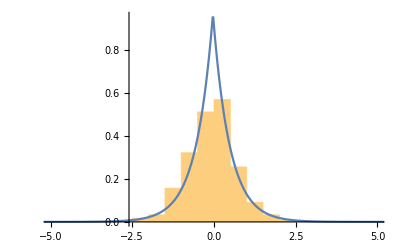

Period=4,9

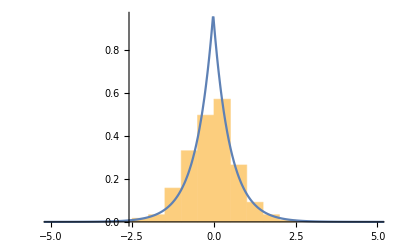

Period=4,10

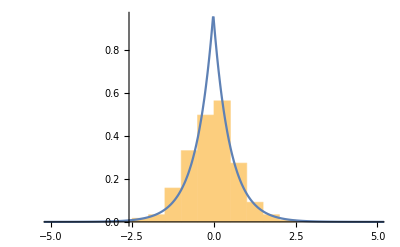

Period=5,1

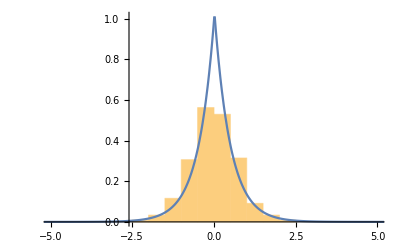

Period=5,2

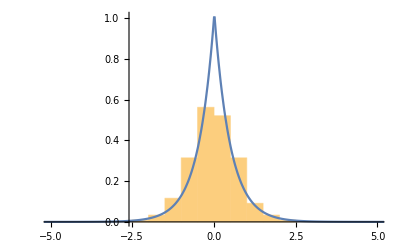

Period=5,3

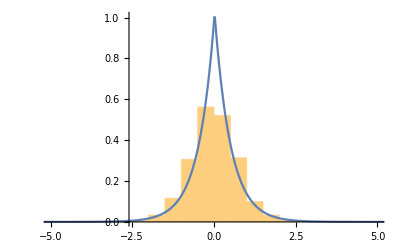

Period=5,4

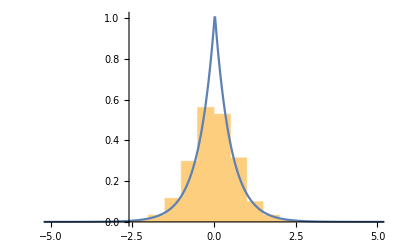

Period=5,5

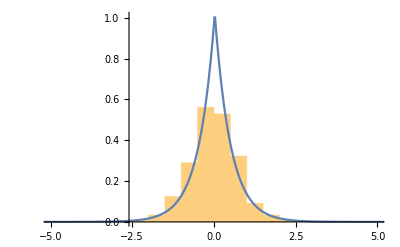

Period=5,6

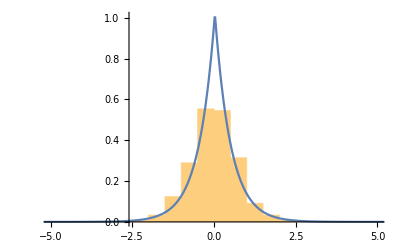

Period=5,7

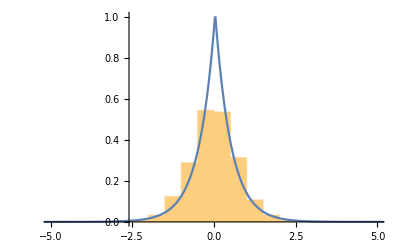

Period=5,8

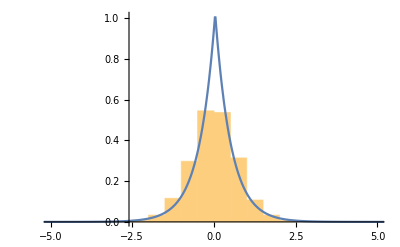

Period=5,9

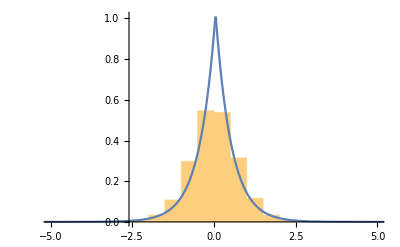

Period=5,10

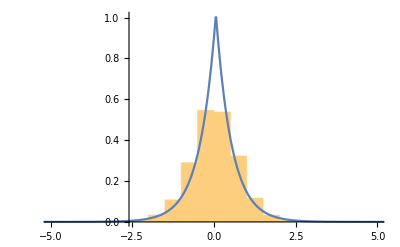

Period=6,1

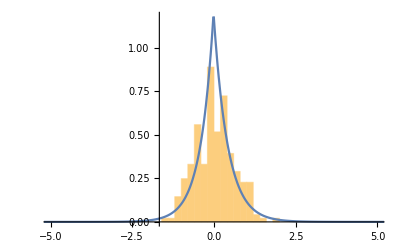

Period=6,2

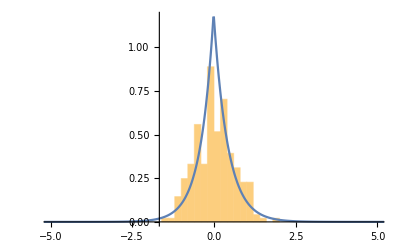

Period=6,3

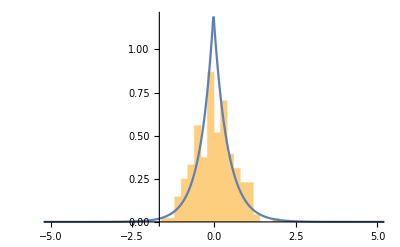

Period=6,4

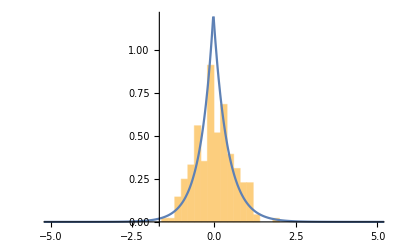

Period=6,5

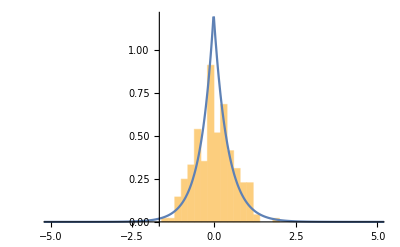

Period=6,6

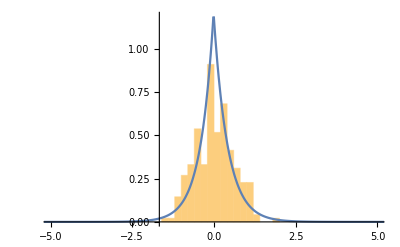

Period=6,7

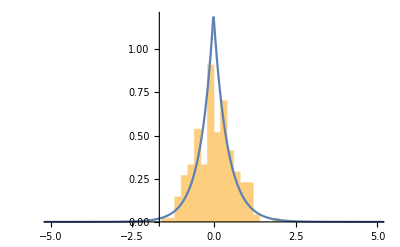

Period=6,8

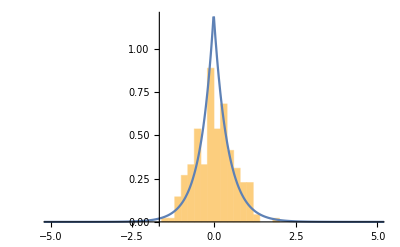

Period=6,9

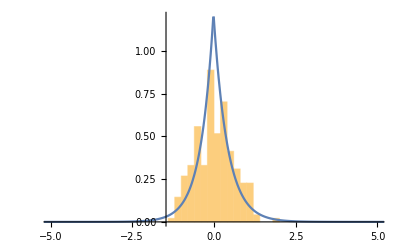

Period=6,10

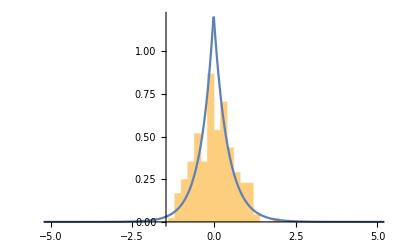

Period=7,1

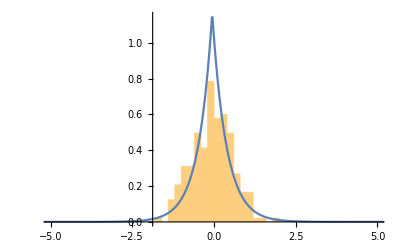

Period=7,2

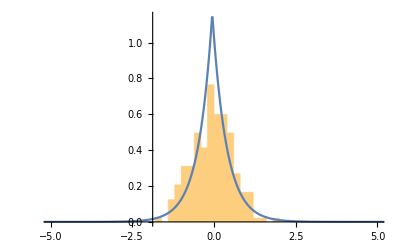

Period=7,3

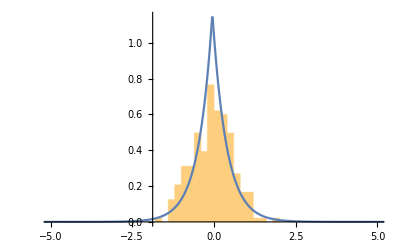

Period=7,4

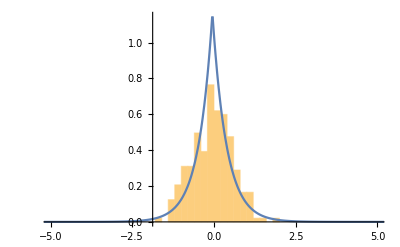

Period=7,5

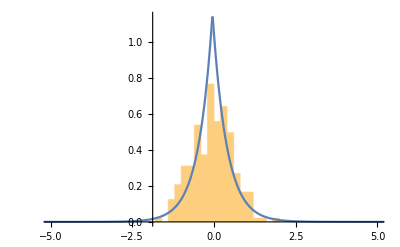

Period=7,6

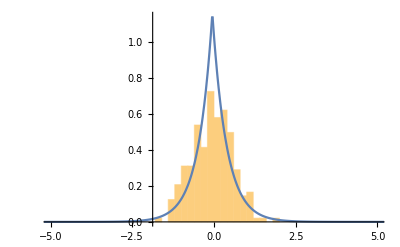

Period=7,7

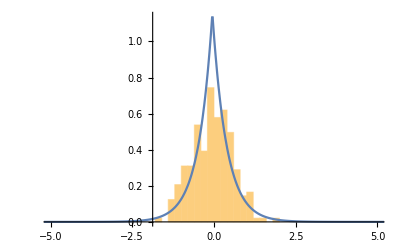

Period=7,8

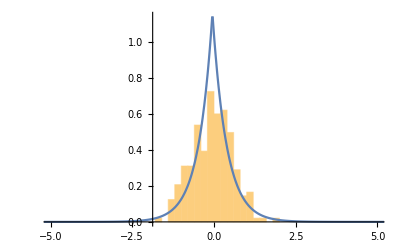

Period=7,9

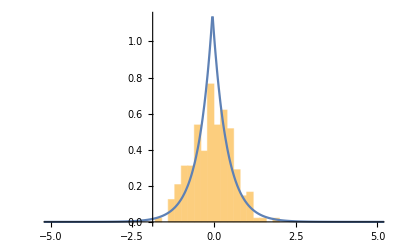

Period=7,10

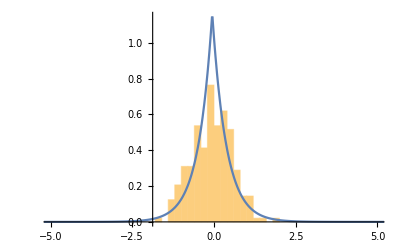

Period=8,1

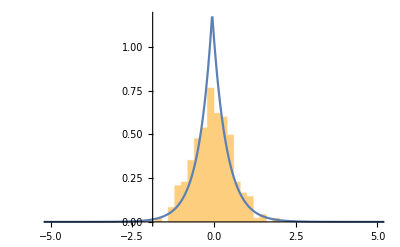

Period=8,2

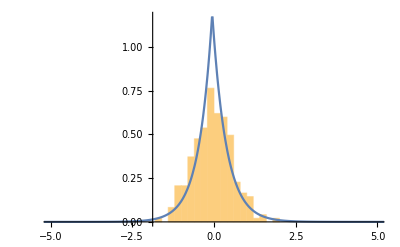

Period=8,3

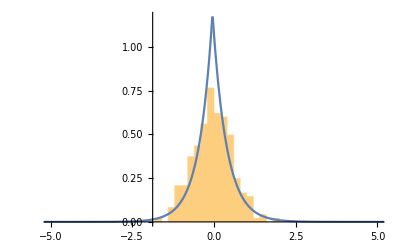

Period=8,4

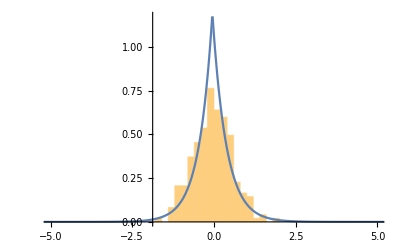

Period=8,5

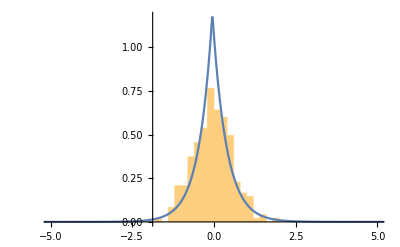

Period=8,6

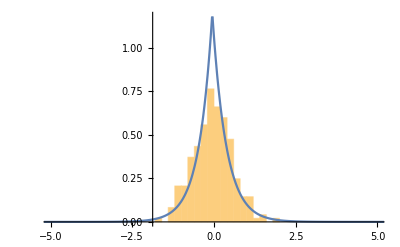

Period=8,7

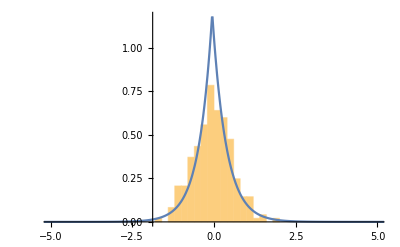

Period=8,8

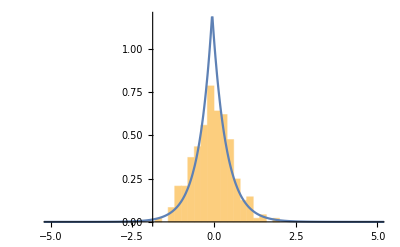

Period=8,9

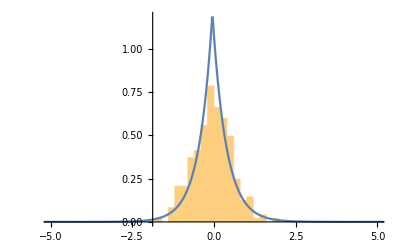

Period=8,10

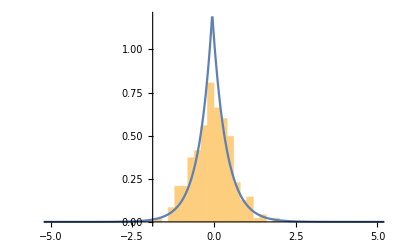

Period=9,1

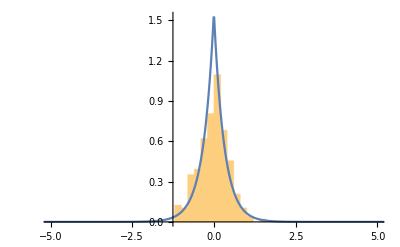

Period=9,2

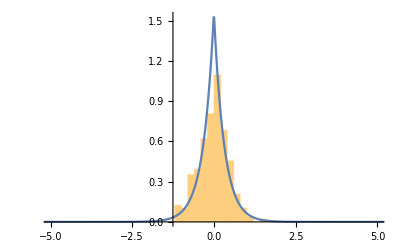

Period=9,3

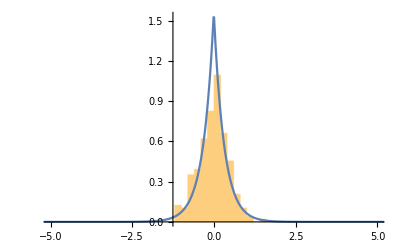

Period=9,4

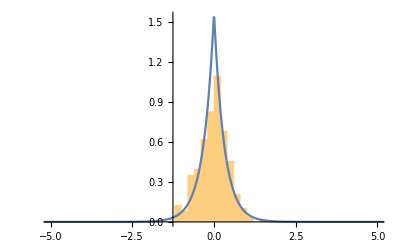

Period=9,5

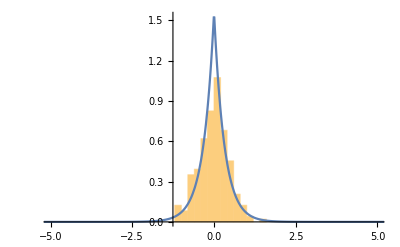

Period=9,6

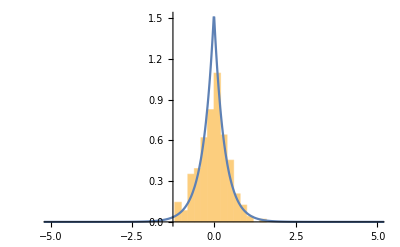

Period=9,7

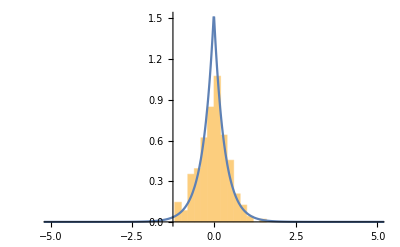

Period=9,8

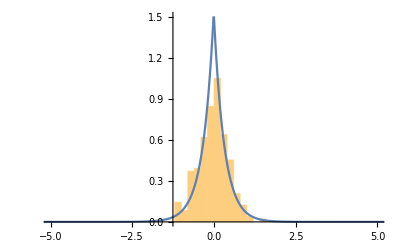

Period=9,9

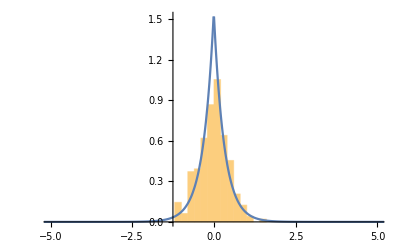

Period=9,10

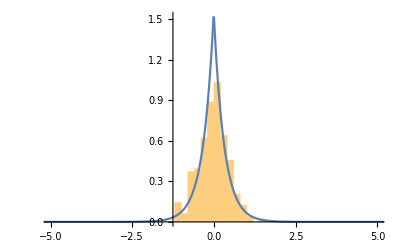

Period=10,1

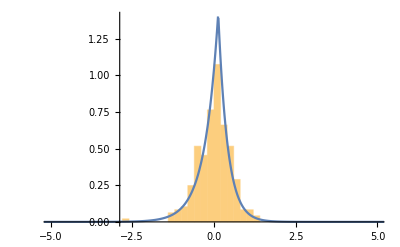

Period=10,2

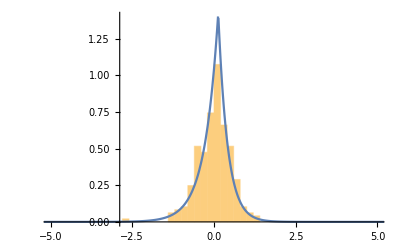

Period=10,3

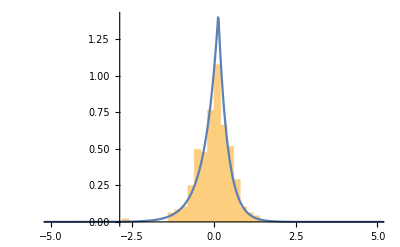

Period=10,4

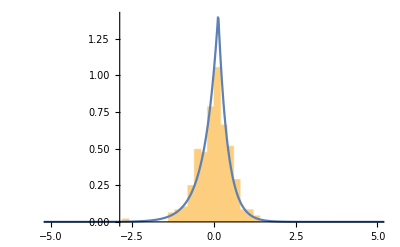

Period=10,5

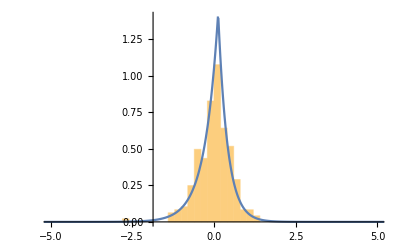

Period=10,6

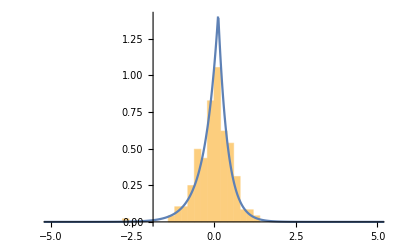

Period=10,7

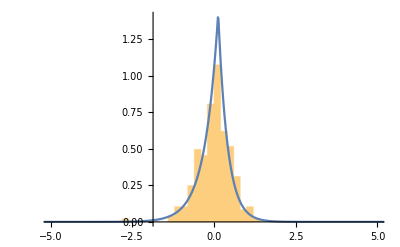

Period=10,8

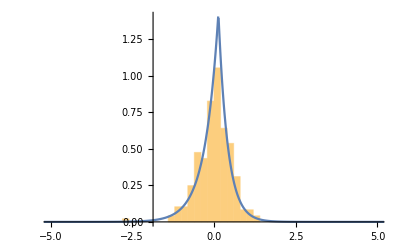

Period=10,9

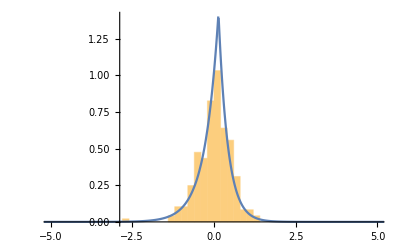

Period=10,10

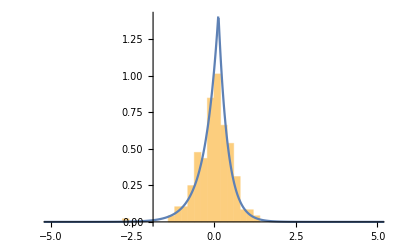

Period=11,1

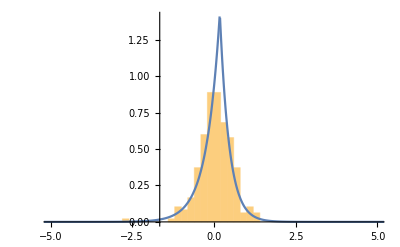

Period=11,2

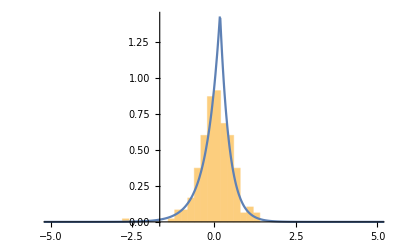

Period=11,3

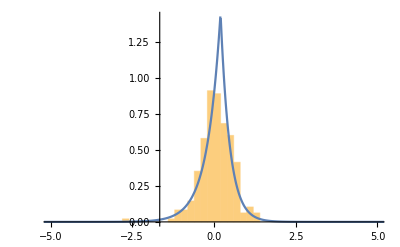

Period=11,4

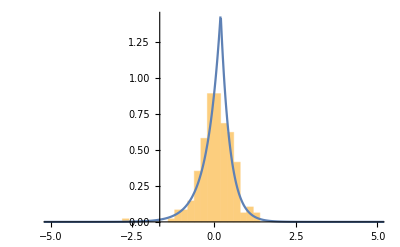

Period=11,5

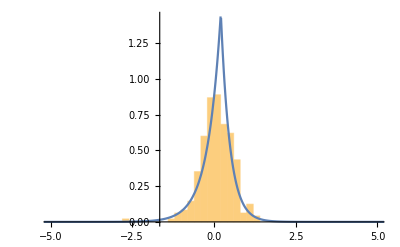

Period=11,6

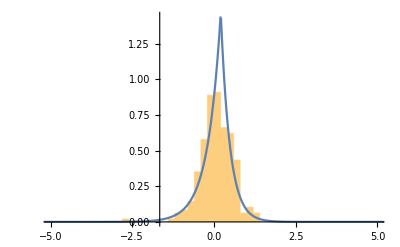

Period=11,7

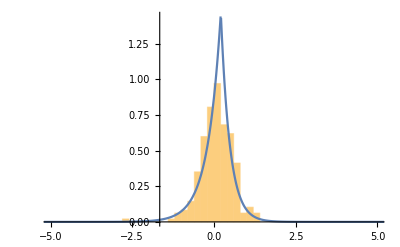

Period=11,8

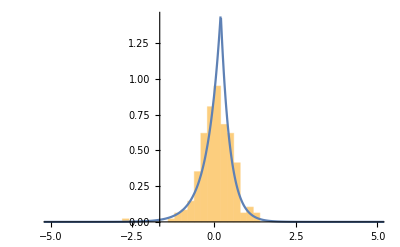

Period=11,9

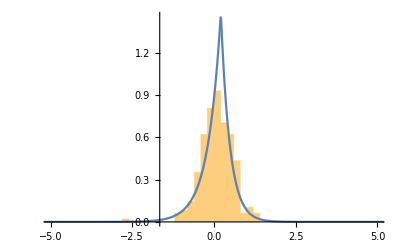

Period=11,10

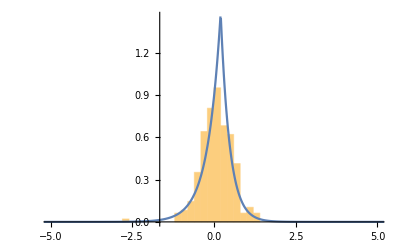

Period=12,1

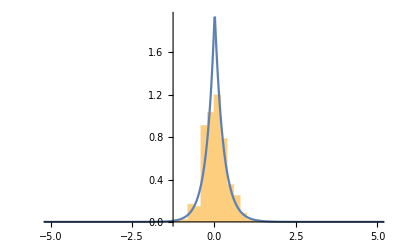

Period=12,2

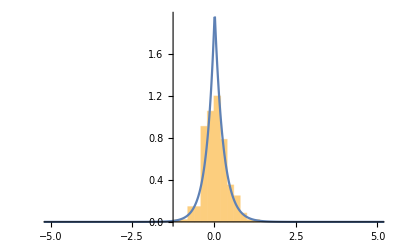

Period=12,3

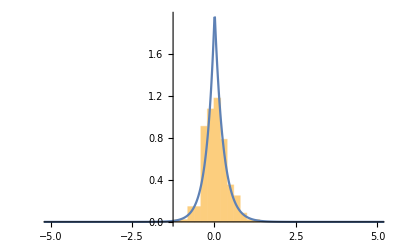

Period=12,4

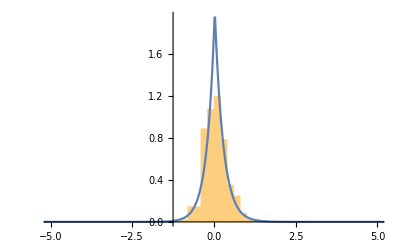

Period=12,5

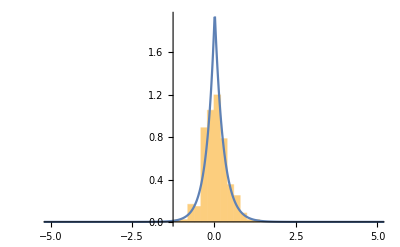

Period=12,6

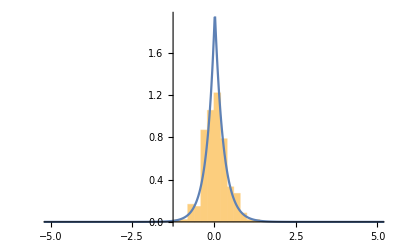

Period=12,7

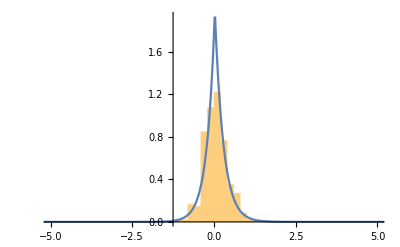

Period=12,8

-Graphics-

Period=12,9

-Graphics-

Period=12,10

-Graphics-

Period=13,1

-Graphics-

Period=13,2

-Graphics-

Period=13,3

-Graphics-

Period=13,4

-Graphics-

Period=13,5

-Graphics-

Period=13,6

-Graphics-

Period=13,7

-Graphics-

Period=13,8

-Graphics-

Period=13,9

-Graphics-

Period=13,10

-Graphics-

Period=14,1

-Graphics-

Period=14,2

-Graphics-

Period=14,3

-Graphics-

Period=14,4

-Graphics-

Period=14,5

-Graphics-

Period=14,6

-Graphics-

Period=14,7

-Graphics-

Period=14,8

-Graphics-

Period=14,9

-Graphics-

Period=14,10

-Graphics-

Period=15,1

-Graphics-

Period=15,2

-Graphics-

Period=15,3

-Graphics-

Period=15,4

-Graphics-

Period=15,5

-Graphics-

Period=15,6

-Graphics-

Period=15,7

-Graphics-

Period=15,8

-Graphics-

Period=15,9

-Graphics-

Period=15,10

-Graphics-

```mathematica
For[n=1,n<16,n++,
For[j=1,j<11,j++,
Print["Period=",n,",",j];
Print[Show[Histogram[Subscript[L1, n,j],Automatic,"ProbabilityDensity"],Plot[Subscript[F1, n,j],{x,-10,10},PlotRange->{Full,Full}],PlotRange->{{-5,5},All}]]]]
```

```mathematica
For[n=1,n<16,n++,
For[j=1,j<11,j++,
Subscript[F2, n,j]=Function[x,((2*Exp[Subscript[θ2, n,j]*(x-Subscript[m2, n,j])/Subscript[σ2, n,j]^2])/(Subscript[σ2, n,j]*Sqrt[2*Pi]*Gamma[1]))*((x-Subscript[m2, n,j])^2/(2*Subscript[σ2, n,j]^2+Subscript[θ2, n,j]^2))^0.25*BesselK[0.5,Sqrt[(x-Subscript[m2, n,j])^2*(2*Subscript[σ2, n,j]^2+Subscript[θ2, n,j]^2)]/Subscript[σ2, n,j]^2]][x];
Subscript[𝒟1, n,j]=ProbabilityDistribution[Subscript[F1, n,j],{x,-Infinity,Infinity}];
Subscript[𝒟2, n,j]=ProbabilityDistribution[Subscript[F2, n,j],{x,-Infinity,Infinity}]]]
```

```mathematica
For[n=1,n<16,n++,
For[j=1,j<11,j++,
Print["Period=",n,",",j];
Print[Show[Histogram[Subscript[L2, n,j],Automatic,"ProbabilityDensity"],Plot[Subscript[F2, n,j],{x,-10,10},PlotRange->{Full,Full}],PlotRange->{{-5,5},All}]]]]
```

Period=1,1

-Graphics-

Period=1,2

-Graphics-

Period=1,3

-Graphics-

Period=1,4

-Graphics-

Period=1,5

-Graphics-

Period=1,6

-Graphics-

Period=1,7

-Graphics-

Period=1,8

-Graphics-

Period=1,9

-Graphics-

Period=1,10

-Graphics-

Period=2,1

-Graphics-

Period=2,2

-Graphics-

Period=2,3

-Graphics-

Period=2,4

-Graphics-

Period=2,5

-Graphics-

Period=2,6

-Graphics-

Period=2,7

-Graphics-

Period=2,8

-Graphics-

Period=2,9

-Graphics-

Period=2,10

-Graphics-

Period=3,1

-Graphics-

Period=3,2

-Graphics-

Period=3,3

-Graphics-

Period=3,4

-Graphics-

Period=3,5

-Graphics-

Period=3,6

-Graphics-

Period=3,7

-Graphics-

Period=3,8

-Graphics-

Period=3,9

-Graphics-

Period=3,10

-Graphics-

Period=4,1

-Graphics-

Period=4,2

-Graphics-

Period=4,3

-Graphics-

Period=4,4

-Graphics-

Period=4,5

-Graphics-

Period=4,6

-Graphics-

Period=4,7

-Graphics-

Period=4,8

-Graphics-

Period=4,9

-Graphics-

Period=4,10

-Graphics-

Period=5,1

-Graphics-

Period=5,2

-Graphics-

Period=5,3

-Graphics-

Period=5,4

-Graphics-

Period=5,5

-Graphics-

Period=5,6

-Graphics-

Period=5,7

-Graphics-

Period=5,8

-Graphics-

Period=5,9

-Graphics-

Period=5,10

-Graphics-

Period=6,1

-Graphics-

Period=6,2

-Graphics-

Period=6,3

-Graphics-

Period=6,4

-Graphics-

Period=6,5

-Graphics-

Period=6,6

-Graphics-

Period=6,7

-Graphics-

Period=6,8

-Graphics-

Period=6,9

-Graphics-

Period=6,10

-Graphics-

Period=7,1

-Graphics-

Period=7,2

-Graphics-

Period=7,3

-Graphics-

Period=7,4

-Graphics-

Period=7,5

-Graphics-

Period=7,6

-Graphics-

Period=7,7

-Graphics-

Period=7,8

-Graphics-

Period=7,9

-Graphics-

Period=7,10

-Graphics-

Period=8,1

-Graphics-

Period=8,2

-Graphics-

Period=8,3

-Graphics-

Period=8,4

-Graphics-

Period=8,5

-Graphics-

Period=8,6

-Graphics-

Period=8,7

-Graphics-

Period=8,8

-Graphics-

Period=8,9

-Graphics-

Period=8,10

-Graphics-

Period=9,1

-Graphics-

Period=9,2

-Graphics-

Period=9,3

-Graphics-

Period=9,4

-Graphics-

Period=9,5

-Graphics-

Period=9,6

-Graphics-

Period=9,7

-Graphics-

Period=9,8

-Graphics-

Period=9,9

-Graphics-

Period=9,10

-Graphics-

Period=10,1

-Graphics-

Period=10,2

-Graphics-

Period=10,3

-Graphics-

Period=10,4

-Graphics-

Period=10,5

-Graphics-

Period=10,6

-Graphics-

Period=10,7

-Graphics-

Period=10,8

-Graphics-

Period=10,9

-Graphics-

Period=10,10

-Graphics-

Period=11,1

-Graphics-

Period=11,2

-Graphics-

Period=11,3

-Graphics-

Period=11,4

-Graphics-

Period=11,5

-Graphics-

Period=11,6

-Graphics-

Period=11,7

-Graphics-

Period=11,8

-Graphics-

Period=11,9

-Graphics-

Period=11,10

-Graphics-

Period=12,1

-Graphics-

Period=12,2

-Graphics-

Period=12,3

-Graphics-

Period=12,4

-Graphics-

Period=12,5

-Graphics-

Period=12,6

-Graphics-

Period=12,7

-Graphics-

Period=12,8

-Graphics-

Period=12,9

-Graphics-

Period=12,10

-Graphics-

Period=13,1

-Graphics-

Period=13,2

-Graphics-

Period=13,3

-Graphics-

Period=13,4

-Graphics-

Period=13,5

-Graphics-

Period=13,6

-Graphics-

Period=13,7

-Graphics-

Period=13,8

-Graphics-

Period=13,9

-Graphics-

Period=13,10

-Graphics-

Period=14,1

-Graphics-

Period=14,2

-Graphics-

Period=14,3

-Graphics-

Period=14,4

-Graphics-

Period=14,5

-Graphics-

Period=14,6

-Graphics-

Period=14,7

-Graphics-

Period=14,8

-Graphics-

Period=14,9

-Graphics-

Period=14,10

-Graphics-

Period=15,1

-Graphics-

Period=15,2

-Graphics-

Period=15,3

-Graphics-

Period=15,4

-Graphics-

Period=15,5

-Graphics-

Period=15,6

-Graphics-

Period=15,7

-Graphics-

Period=15,8

-Graphics-

Period=15,9

-Graphics-

Period=15,10

-Graphics-

```mathematica
For[n=1,n<16,n++,
For[j=1,j<11,j++,
Print["Period=",n,",",j];
Print["GBP/USD"];
Print[DistributionFitTest[Subscript[L1, n,j],Subscript[𝒟1, n,j],"PearsonChiSquare"]];
Print["EUR/USD"];
Print[DistributionFitTest[Subscript[L2, n,j],Subscript[𝒟2, n,j],"PearsonChiSquare"]]]]
```

Period=1,1

GBP/USD

0.0732644

EUR/USD

0.971247

Period=1,2

GBP/USD

0.123996

EUR/USD

0.989801

Period=1,3

GBP/USD

0.0504307

EUR/USD

0.986813

Period=1,4

GBP/USD

0.0656175

EUR/USD

0.99109

Period=1,5

GBP/USD

0.20046

EUR/USD

0.992252

Period=1,6

GBP/USD

0.156099

EUR/USD

0.971247

Period=1,7

GBP/USD

0.111999

EUR/USD

0.978978

Period=1,8

GBP/USD

0.166393

EUR/USD

0.994229

Period=1,9

GBP/USD

0.151144

EUR/USD

0.971247

Period=1,10

GBP/USD

0.171736

EUR/USD

0.995059

Period=2,1

GBP/USD

0.350292

EUR/USD

0.0586766

Period=2,2

GBP/USD

0.350292

EUR/USD

0.0787809

Period=2,3

GBP/USD

0.188563

EUR/USD

0.0732644

Period=2,4

GBP/USD

0.253641

EUR/USD

0.0328131

Period=2,5

GBP/USD

0.32428

EUR/USD

0.0355297

Period=2,6

GBP/USD

0.32428

EUR/USD

0.0544158

Period=2,7

GBP/USD

0.268354

EUR/USD

0.0257552

Period=2,8

GBP/USD

0.332818

EUR/USD

0.0192898

Period=2,9

GBP/USD

0.444887

EUR/USD

0.0209651

Period=2,10

GBP/USD

0.454926

EUR/USD

0.0209651

Period=3,1

GBP/USD

0.0101579

EUR/USD

0.350292

Period=3,2

GBP/USD

0.0143518

EUR/USD

0.332818

Period=3,3

GBP/USD

0.00544687

EUR/USD

0.548561

Period=3,4

GBP/USD

0.0120861

EUR/USD

0.299477

Period=3,5

GBP/USD

0.00745926

EUR/USD

0.268354

Period=3,6

GBP/USD

0.027937

EUR/USD

0.206616

Period=3,7

GBP/USD

0.0227733

EUR/USD

0.14161

Period=3,8

GBP/USD

0.00623676

EUR/USD

0.0415796

Period=3,9

GBP/USD

0.00454014

EUR/USD

0.048537

Period=3,10

GBP/USD

0.00377794

EUR/USD

0.0680854

Period=4,1

GBP/USD

0.00344411

EUR/USD

0.108221

Period=4,2

GBP/USD

0.0156273

EUR/USD

0.0355297

Period=4,3

GBP/USD

0.00236934

EUR/USD

0.0399862

Period=4,4

GBP/USD

0.0237302

EUR/USD

0.027937

Period=4,5

GBP/USD

0.0268259

EUR/USD

0.027937

Period=4,6

GBP/USD

0.0156273

EUR/USD

0.030286

Period=4,7

GBP/USD

0.00972295

EUR/USD

0.0432297

Period=4,8

GBP/USD

0.0268259

EUR/USD

0.0315266

Period=4,9

GBP/USD

0.0432297

EUR/USD

0.0131737

Period=4,10

GBP/USD

0.0504307

EUR/USD

0.0257552

Period=5,1

GBP/USD

0.00115594

EUR/USD

0.00433694

Period=5,2

GBP/USD

0.000998961

EUR/USD

0.00344411

Period=5,3

GBP/USD

0.000409675

EUR/USD

0.0328131

Period=5,4

GBP/USD

0.00544687

EUR/USD

0.0201114

Period=5,5

GBP/USD

0.0014717

EUR/USD

0.027937

Period=5,6

GBP/USD

0.00236934

EUR/USD

0.0315266

Period=5,7

GBP/USD

0.00779842

EUR/USD

0.0156273

Period=5,8

GBP/USD

0.00713404

EUR/USD

0.013751

Period=5,9

GBP/USD

0.0120861

EUR/USD

0.0586766

Period=5,10

GBP/USD

0.00745926

EUR/USD

0.0257552

Period=6,1

GBP/USD

0.00713404

EUR/USD

0.123996

Period=6,2

GBP/USD

0.00713404

EUR/USD

0.0759794

Period=6,3

GBP/USD

0.00852072

EUR/USD

0.0656175

Period=6,4

GBP/USD

0.00475235

EUR/USD

0.0504307

Period=6,5

GBP/USD

0.0184993

EUR/USD

0.063228

Period=6,6

GBP/USD

0.013751

EUR/USD

0.0163038

Period=6,7

GBP/USD

0.00745926

EUR/USD

0.0732644

Period=6,8

GBP/USD

0.0201114

EUR/USD

0.104549

Period=6,9

GBP/USD

0.0156273

EUR/USD

0.0877243

Period=6,10

GBP/USD

0.00930556

EUR/USD

0.123996

Period=7,1

GBP/USD

0.00169936

EUR/USD

0.0247237

Period=7,2

GBP/USD

0.00110114

EUR/USD

0.0315266

Period=7,3

GBP/USD

0.00196061

EUR/USD

0.0399862

Period=7,4

GBP/USD

0.00196061

EUR/USD

0.0227733

Period=7,5

GBP/USD

0.00196061

EUR/USD

0.0227733

Period=7,6

GBP/USD

0.00133654

EUR/USD

0.0467067

Period=7,7

GBP/USD

0.00196061

EUR/USD

0.0449382

Period=7,8

GBP/USD

0.00236934

EUR/USD

0.0384477

Period=7,9

GBP/USD

0.00226011

EUR/USD

0.0399862

Period=7,10

GBP/USD

0.000181673

EUR/USD

0.0586766

Period=8,1

GBP/USD

0.0586766

EUR/USD

0.495907

Period=8,2

GBP/USD

0.0384477

EUR/USD

0.444887

Period=8,3

GBP/USD

0.0209651

EUR/USD

0.527353

Period=8,4

GBP/USD

0.0415796

EUR/USD

0.569901

Period=8,5

GBP/USD

0.0415796

EUR/USD

0.676439

Period=8,6

GBP/USD

0.0586766

EUR/USD

0.475262

Period=8,7

GBP/USD

0.0787809

EUR/USD

0.623437

Period=8,8

GBP/USD

0.0467067

EUR/USD

0.717746

Period=8,9

GBP/USD

0.0227733

EUR/USD

0.591315

Period=8,10

GBP/USD

0.0449382

EUR/USD

0.77659

Period=9,1

GBP/USD

0.0908918

EUR/USD

0.161181

Period=9,2

GBP/USD

0.0816709

EUR/USD

0.111999

Period=9,3

GBP/USD

0.0732644

EUR/USD

0.132565

Period=9,4

GBP/USD

0.0732644

EUR/USD

0.246498

Period=9,5

GBP/USD

0.094156

EUR/USD

0.188563

Period=9,6

GBP/USD

0.156099

EUR/USD

0.291486

Period=9,7

GBP/USD

0.151144

EUR/USD

0.21291

Period=9,8

GBP/USD

0.0565108

EUR/USD

0.219345

Period=9,9

GBP/USD

0.111999

EUR/USD

0.359222

Period=9,10

GBP/USD

0.146314

EUR/USD

0.359222

Period=10,1

GBP/USD

0.32428

EUR/USD

0.485549

Period=10,2

GBP/USD

0.291486

EUR/USD

0.548561

Period=10,3

GBP/USD

0.444887

EUR/USD

0.495907

Period=10,4

GBP/USD

0.34149

EUR/USD

0.537937

Period=10,5

GBP/USD

0.299477

EUR/USD

0.386758

Period=10,6

GBP/USD

0.506332

EUR/USD

0.465053

Period=10,7

GBP/USD

0.60203

EUR/USD

0.283634

Period=10,8

GBP/USD

0.727848

EUR/USD

0.315875

Period=10,9

GBP/USD

0.61274

EUR/USD

0.527353

Period=10,10

GBP/USD

0.665932

EUR/USD

0.315875

Period=11,1

GBP/USD

0.332818

EUR/USD

0.097519

Period=11,2

GBP/USD

0.396175

EUR/USD

0.0656175

Period=11,3

GBP/USD

0.425093

EUR/USD

0.177211

Period=11,4

GBP/USD

0.225921

EUR/USD

0.166393

Period=11,5

GBP/USD

0.156099

EUR/USD

0.21291

Period=11,6

GBP/USD

0.111999

EUR/USD

0.20046

Period=11,7

GBP/USD

0.0586766

EUR/USD

0.171736

Period=11,8

GBP/USD

0.100983

EUR/USD

0.137027

Period=11,9

GBP/USD

0.0565108

EUR/USD

0.225921

Period=11,10

GBP/USD

0.0170073

EUR/USD

0.188563

Period=12,1

GBP/USD

0.0544158

EUR/USD

0.465053

Period=12,2

GBP/USD

0.060915

EUR/USD

0.465053

Period=12,3

GBP/USD

0.0565108

EUR/USD

0.61274

Period=12,4

GBP/USD

0.0399862

EUR/USD

0.676439

Period=12,5

GBP/USD

0.0170073

EUR/USD

0.707545

Period=12,6

GBP/USD

0.0399862

EUR/USD

0.804124

Period=12,7

GBP/USD

0.0218521

EUR/USD

0.876825

Period=12,8

GBP/USD

0.0355297

EUR/USD

0.883861

Period=12,9

GBP/USD

0.0846513

EUR/USD

0.757481

Period=12,10

GBP/USD

0.0706337

EUR/USD

0.821639

Period=13,1

GBP/USD

0.283634

EUR/USD

0.64476

Period=13,2

GBP/USD

0.299477

EUR/USD

0.795107

Period=13,3

GBP/USD

0.291486

EUR/USD

0.785927

Period=13,4

GBP/USD

0.485549

EUR/USD

0.846514

Period=13,5

GBP/USD

0.307608

EUR/USD

0.676439

Period=13,6

GBP/USD

0.18282

EUR/USD

0.757481

Period=13,7

GBP/USD

0.111999

EUR/USD

0.838417

Period=13,8

GBP/USD

0.206616

EUR/USD

0.968282

Period=13,9

GBP/USD

0.132565

EUR/USD

0.989801

Period=13,10

GBP/USD

0.18282

EUR/USD

0.971247

Period=14,1

GBP/USD

0.0787809

EUR/USD

0.495907

Period=14,2

GBP/USD

0.094156

EUR/USD

0.676439

Period=14,3

GBP/USD

0.132565

EUR/USD

0.425093

Period=14,4

GBP/USD

0.030286

EUR/USD

0.897256

Period=14,5

GBP/USD

0.0504307

EUR/USD

0.862094

Period=14,6

GBP/USD

0.0369628

EUR/USD

0.81297

Period=14,7

GBP/USD

0.0328131

EUR/USD

0.795107

Period=14,8

GBP/USD

0.0467067

EUR/USD

0.846514

Period=14,9

GBP/USD

0.108221

EUR/USD

0.737844

Period=14,10

GBP/USD

0.123996

EUR/USD

0.737844

Period=15,1

GBP/USD

0.104549

EUR/USD

0.883861

Period=15,2

GBP/USD

0.115886

EUR/USD

0.971247

Period=15,3

GBP/USD

0.188563

EUR/USD

0.968282

Period=15,4

GBP/USD

0.097519

EUR/USD

0.968282

Period=15,5

GBP/USD

0.132565

EUR/USD

0.946037

Period=15,6

GBP/USD

0.100983

EUR/USD

0.915621

Period=15,7

GBP/USD

0.123996

EUR/USD

0.90361

Period=15,8

GBP/USD

0.146314

EUR/USD

0.862094

Period=15,9

GBP/USD

0.119885

EUR/USD

0.747725

Period=15,10

GBP/USD

0.0399862

EUR/USD

0.869568

```mathematica
For[n=1,n<16,n++,
For[j=1,j<11,j++,
Subscript[R12, n,j]=Sin[Pi*KendallTau[Subscript[L1, n,j],Subscript[L2, n,j]]/2];
Subscript[R, n,j]={{1,Subscript[R12, n,j]},{Subscript[R12, n,j],1}}]]
```

```mathematica
For[n=1,n<16,n++,
For[j=1,j<11,j++,
Subscript[data, n,j]=Table[{Subscript[L1, n,j][[i]],Subscript[L2, n,j][[i]]},{i,1,242}]]]
```

```mathematica
n=1;
For[j=1,j<11,j++,
Print["Period=",n,",",j];
Print[EstimatedDistribution[Subscript[data, n,j],CopulaDistribution[{"MultivariateT",Subscript[R, n,j],Subscript[o, n,j]},{StudentTDistribution[Subscript[o, n,j]],StudentTDistribution[Subscript[o, n,j]]}],ParameterEstimator->"MaximumLikelihood"]]]
```

Period=1,1

CopulaDistribution[{MultivariateT,{{1,0.647584},{0.647584,1}},8.61964},{StudentTDistribution[8.61964],StudentTDistribution[8.61964]}]

Period=1,2

CopulaDistribution[{MultivariateT,{{1,0.657219},{0.657219,1}},8.09335},{StudentTDistribution[8.09335],StudentTDistribution[8.09335]}]

Period=1,3

CopulaDistribution[{MultivariateT,{{1,0.661027},{0.661027,1}},7.99737},{StudentTDistribution[7.99737],StudentTDistribution[7.99737]}]

Period=1,4

CopulaDistribution[{MultivariateT,{{1,0.655105},{0.655105,1}},8.06154},{StudentTDistribution[8.06154],StudentTDistribution[8.06154]}]

Period=1,5

CopulaDistribution[{MultivariateT,{{1,0.660865},{0.660865,1}},7.81326},{StudentTDistribution[7.81326],StudentTDistribution[7.81326]}]

Period=1,6

CopulaDistribution[{MultivariateT,{{1,0.661996},{0.661996,1}},7.76482},{StudentTDistribution[7.76482],StudentTDistribution[7.76482]}]

Period=1,7

CopulaDistribution[{MultivariateT,{{1,0.657706},{0.657706,1}},7.77187},{StudentTDistribution[7.77187],StudentTDistribution[7.77187]}]

Period=1,8

CopulaDistribution[{MultivariateT,{{1,0.659327},{0.659327,1}},7.73841},{StudentTDistribution[7.73841],StudentTDistribution[7.73841]}]

Period=1,9

CopulaDistribution[{MultivariateT,{{1,0.661188},{0.661188,1}},7.69966},{StudentTDistribution[7.69966],StudentTDistribution[7.69966]}]

Period=1,10

CopulaDistribution[{MultivariateT,{{1,0.665461},{0.665461,1}},7.62058},{StudentTDistribution[7.62058],StudentTDistribution[7.62058]}]

```mathematica
Subscript[v, 1,1]=8.619637784274104;
Subscript[v, 1,2]=8.093352194641847;
Subscript[v, 1,3]=7.997367630983822;
Subscript[v, 1,4]=8.06153518391046;
Subscript[v, 1,5]=7.813261103646121;
Subscript[v, 1,6]=7.764815802743605;
Subscript[v, 1,7]=7.771866416186959;
Subscript[v, 1,8]=7.738407321932989;
Subscript[v, 1,9]=7.699664078759734;
Subscript[v, 1,10]=7.620584261920592;
```

```mathematica
For[j=1,j<11,j++,
Print[EstimatedDistribution[Subscript[data, 9,j],CopulaDistribution[{"MultivariateT",Subscript[R, 9,j],Subscript[v, 9,j]},{StudentTDistribution[Subscript[v, 9,j]],StudentTDistribution[Subscript[v, 9,j]]}],ParameterEstimator->"MaximumLikelihood"]]]
```

CopulaDistribution[{MultivariateT,{{1,0.672428},{0.672428,1}},83706.7},{StudentTDistribution[83706.7],StudentTDistribution[83706.7]}]

CopulaDistribution[{MultivariateT,{{1,0.669312},{0.669312,1}},79959.6},{StudentTDistribution[79959.6],StudentTDistribution[79959.6]}]

CopulaDistribution[{MultivariateT,{{1,0.668271},{0.668271,1}},53687.7},{StudentTDistribution[53687.7],StudentTDistribution[53687.7]}]

CopulaDistribution[{MultivariateT,{{1,0.656244},{0.656244,1}},4462.73},{StudentTDistribution[4462.73],StudentTDistribution[4462.73]}]

CopulaDistribution[{MultivariateT,{{1,0.652741},{0.652741,1}},4294.17},{StudentTDistribution[4294.17],StudentTDistribution[4294.17]}]

CopulaDistribution[{MultivariateT,{{1,0.655349},{0.655349,1}},10999.1},{StudentTDistribution[10999.1],StudentTDistribution[10999.1]}]

CopulaDistribution[{MultivariateT,{{1,0.649552},{0.649552,1}},8549.76},{StudentTDistribution[8549.76],StudentTDistribution[8549.76]}]

CopulaDistribution[{MultivariateT,{{1,0.652986},{0.652986,1}},399103.},{StudentTDistribution[399103.],StudentTDistribution[399103.]}]

CopulaDistribution[{MultivariateT,{{1,0.652415},{0.652415,1}},15854.7},{StudentTDistribution[15854.7],StudentTDistribution[15854.7]}]

CopulaDistribution[{MultivariateT,{{1,0.651761},{0.651761,1}},5323.15},{StudentTDistribution[5323.15],StudentTDistribution[5323.15]}]

```mathematica
Subscript[v, 9,1]=83706.69849402862;
Subscript[v, 9,2]=79959.62517428656;
Subscript[v, 9,3]=53687.70943330998;
Subscript[v, 9,4]=4462.726884669605;
Subscript[v, 9,5]=4294.174877793377;
Subscript[v, 9,6]=10999.075132659358;
Subscript[v, 9,7]=8549.758727226601;
Subscript[v, 9,8]=399102.95704218285;
Subscript[v, 9,9]=15854.722608904824;
Subscript[v, 9,10]=5323.146701891072;
```

```mathematica
For[j=1,j<11,j++,
Print[EstimatedDistribution[Subscript[data, 10,j],CopulaDistribution[{"MultivariateT",Subscript[R, 10,j],Subscript[v, 10,j]},{StudentTDistribution[Subscript[v, 10,j]],StudentTDistribution[Subscript[v, 10,j]]}],ParameterEstimator->"MaximumLikelihood"]]]
```

CopulaDistribution[{MultivariateT,{{1,0.643388},{0.643388,1}},40005.7},{StudentTDistribution[40005.7],StudentTDistribution[40005.7]}]

CopulaDistribution[{MultivariateT,{{1,0.644624},{0.644624,1}},52260.5},{StudentTDistribution[52260.5],StudentTDistribution[52260.5]}]

CopulaDistribution[{MultivariateT,{{1,0.642976},{0.642976,1}},116737.},{StudentTDistribution[116737.],StudentTDistribution[116737.]}]

CopulaDistribution[{MultivariateT,{{1,0.642976},{0.642976,1}},264118.},{StudentTDistribution[264118.],StudentTDistribution[264118.]}]

CopulaDistribution[{MultivariateT,{{1,0.639255},{0.639255,1}},305850.},{StudentTDistribution[305850.],StudentTDistribution[305850.]}]

CopulaDistribution[{MultivariateT,{{1,0.63768},{0.63768,1}},49102.2},{StudentTDistribution[49102.2],StudentTDistribution[49102.2]}]

CopulaDistribution[{MultivariateT,{{1,0.632604},{0.632604,1}},55231.6},{StudentTDistribution[55231.6],StudentTDistribution[55231.6]}]

CopulaDistribution[{MultivariateT,{{1,0.633771},{0.633771,1}},27485.9},{StudentTDistribution[27485.9],StudentTDistribution[27485.9]}]

CopulaDistribution[{MultivariateT,{{1,0.634687},{0.634687,1}},5296.05},{StudentTDistribution[5296.05],StudentTDistribution[5296.05]}]

CopulaDistribution[{MultivariateT,{{1,0.63527},{0.63527,1}},374587.},{StudentTDistribution[374587.],StudentTDistribution[374587.]}]

```mathematica
Subscript[v, 10,1]=40005.668993716594;
Subscript[v, 10,2]=52260.491428197536;
Subscript[v, 10,3]=116736.89928279349;
Subscript[v, 10,4]=264118.08941250073;
Subscript[v, 10,5]=305850.36458821304;
Subscript[v, 10,6]=49102.179054895234;
Subscript[v, 10,7]=55231.552818440454;
Subscript[v, 10,8]=27485.87226026184;
Subscript[v, 10,9]=5296.047655937466;
Subscript[v, 10,10]=374586.86450943863;
```

```mathematica
For[j=1,j<11,j++,
Print[EstimatedDistribution[Subscript[data, 11,j],CopulaDistribution[{"MultivariateT",Subscript[R, 11,j],Subscript[v, 11,j]},{StudentTDistribution[Subscript[v, 11,j]],StudentTDistribution[Subscript[v, 11,j]]}],ParameterEstimator->"MaximumLikelihood"]]]
```

CopulaDistribution[{MultivariateT,{{1,0.597011},{0.597011,1}},20271.4},{StudentTDistribution[20271.4],StudentTDistribution[20271.4]}]

CopulaDistribution[{MultivariateT,{{1,0.601496},{0.601496,1}},248728.},{StudentTDistribution[248728.],StudentTDistribution[248728.]}]

CopulaDistribution[{MultivariateT,{{1,0.590771},{0.590771,1}},8995.26},{StudentTDistribution[8995.26],StudentTDistribution[8995.26]}]

CopulaDistribution[{MultivariateT,{{1,0.594069},{0.594069,1}},16761.2},{StudentTDistribution[16761.2],StudentTDistribution[16761.2]}]

CopulaDistribution[{MultivariateT,{{1,0.601324},{0.601324,1}},4515.99},{StudentTDistribution[4515.99],StudentTDistribution[4515.99]}]

CopulaDistribution[{MultivariateT,{{1,0.595974},{0.595974,1}},62447.5},{StudentTDistribution[62447.5],StudentTDistribution[62447.5]}]

CopulaDistribution[{MultivariateT,{{1,0.595108},{0.595108,1}},39064.6},{StudentTDistribution[39064.6],StudentTDistribution[39064.6]}]

CopulaDistribution[{MultivariateT,{{1,0.599601},{0.599601,1}},1.38388×10^6},{StudentTDistribution[1.38388×10^6],StudentTDistribution[1.38388×10^6]}]

CopulaDistribution[{MultivariateT,{{1,0.594415},{0.594415,1}},18370.7},{StudentTDistribution[18370.7],StudentTDistribution[18370.7]}]

CopulaDistribution[{MultivariateT,{{1,0.594069},{0.594069,1}},74053.8},{StudentTDistribution[74053.8],StudentTDistribution[74053.8]}]

```mathematica
Subscript[v, 11,1]=20271.35236712547;
Subscript[v, 11,2]=248727.87159378297;
Subscript[v, 11,3]=8995.257250389624;
Subscript[v, 11,4]=16761.242079406147;
Subscript[v, 11,5]=4515.994290491285;
Subscript[v, 11,6]=62447.456404520366;
Subscript[v, 11,7]=39064.64482060048;
Subscript[v, 11,8]=1.383877138496494*^6;
Subscript[v, 11,9]=18370.66656598629;
Subscript[v, 11,10]=74053.83849971481;
```

```mathematica
For[j=1,j<11,j++,
Print[EstimatedDistribution[Subscript[data, 13,j],CopulaDistribution[{"MultivariateT",Subscript[R, 13,j],Subscript[v, 13,j]},{StudentTDistribution[Subscript[v, 13,j]],StudentTDistribution[Subscript[v, 13,j]]}],ParameterEstimator->"MaximumLikelihood"]]]
```

CopulaDistribution[{MultivariateT,{{1,0.502734},{0.502734,1}},84287.5},{StudentTDistribution[84287.5],StudentTDistribution[84287.5]}]

CopulaDistribution[{MultivariateT,{{1,0.487384},{0.487384,1}},7910.72},{StudentTDistribution[7910.72],StudentTDistribution[7910.72]}]

CopulaDistribution[{MultivariateT,{{1,0.483899},{0.483899,1}},12461.4},{StudentTDistribution[12461.4],StudentTDistribution[12461.4]}]

CopulaDistribution[{MultivariateT,{{1,0.478516},{0.478516,1}},399122.},{StudentTDistribution[399122.],StudentTDistribution[399122.]}]

CopulaDistribution[{MultivariateT,{{1,0.475865},{0.475865,1}},307718.},{StudentTDistribution[307718.],StudentTDistribution[307718.]}]

CopulaDistribution[{MultivariateT,{{1,0.475012},{0.475012,1}},3581.66},{StudentTDistribution[3581.66],StudentTDistribution[3581.66]}]

CopulaDistribution[{MultivariateT,{{1,0.477191},{0.477191,1}},155810.},{StudentTDistribution[155810.],StudentTDistribution[155810.]}]

CopulaDistribution[{MultivariateT,{{1,0.487854},{0.487854,1}},302122.},{StudentTDistribution[302122.],StudentTDistribution[302122.]}]

CopulaDistribution[{MultivariateT,{{1,0.488324},{0.488324,1}},318021.},{StudentTDistribution[318021.],StudentTDistribution[318021.]}]

CopulaDistribution[{MultivariateT,{{1,0.496482},{0.496482,1}},131632.},{StudentTDistribution[131632.],StudentTDistribution[131632.]}]

```mathematica
Subscript[v, 13,1]=84287.46131441888;
Subscript[v, 13,2]=7910.716404973229;
Subscript[v, 13,3]=12461.353330831922;
Subscript[v, 13,4]=399121.55428974924;
Subscript[v, 13,5]=307718.13246612897;
Subscript[v, 13,6]=3581.6577264610373;
Subscript[v, 13,7]=155810.2113939232;
Subscript[v, 13,8]=302121.57354029606;
Subscript[v, 13,9]=318021.2811461081;
Subscript[v, 13,10]=131632.17884134545;
```

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[A, n,j]=CholeskyDecomposition[Subscript[R, n,j]];
Subscript[dist, n,j]=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[Subscript[v, n,j]]];
Subscript[z1, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],1],242];
Subscript[z2, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],2],242];
Subscript[s, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],3],242];
For[i=1,i≤242,i++,
Subscript[s, n,j,i]=Subscript[s, n,j][[i]];
Subscript[y, n,j,i]=Subscript[A, n,j].{Subscript[z1, n,j][[i]],Subscript[z2, n,j][[i]]};
Subscript[x, n,j,i]=Sqrt[Subscript[v, n,j]]/Sqrt[Subscript[s, n,j,i]]*Subscript[y, n,j,i]];
Subscript[x1, n,j]=Table[Subscript[x, n,j,i][[1]],{i,242}];
Subscript[x2, n,j]=Table[Subscript[x, n,j,i][[2]],{i,242}];
Subscript[u1, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x1, n,j]];
Subscript[u2, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x2, n,j]]]
```

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[S1, n,j]=Take[Drop[gbpusd,251+126*(n-1)+j-1],1];
Subscript[S2, n,j]=Take[Drop[eurusd,251+126*(n-1)+j-1],1];
Subscript[pdate, n,j]=Take[Drop[date,252+126*(n-1)+j-1],1];
Subscript[l1, n,j]=InverseCDF[Subscript[𝒟1, n,j],Subscript[u1, n,j]];
Subscript[l2, n,j]=InverseCDF[Subscript[𝒟2, n,j],Subscript[u2, n,j]]]
```

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[forecast1, n,j]=Subscript[S1, n,j]*Exp[-Subscript[k1, n,j]*Subscript[b1, n,j,242]+Subscript[l1, n,j][[242]]/100];
Subscript[forecast2, n,j]=Subscript[S2, n,j]*Exp[-Subscript[k2, n,j]*Subscript[b2, n,j,242]+Subscript[l2, n,j][[242]]/100]];
Subscript[Forecast1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast1, n,j][[1]]},{j,10}];
Subscript[Forecast2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast2, n,j][[1]]},{j,10}];
Subscript[predict1, n]=Take[Drop[GBPUSD,252+126*(n-1)],10];
Subscript[predict2, n]=Take[Drop[EURUSD,252+126*(n-1)],10];
DateListPlot[{Subscript[Forecast1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=9;
For[j=1,j<11,j++,
Subscript[A, n,j]=CholeskyDecomposition[Subscript[R, n,j]];
Subscript[dist, n,j]=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[Subscript[v, n,j]]];
Subscript[z1, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],1],242];
Subscript[z2, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],2],242];
Subscript[s, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],3],242];
For[i=1,i≤242,i++,
Subscript[s, n,j,i]=Subscript[s, n,j][[i]];
Subscript[y, n,j,i]=Subscript[A, n,j].{Subscript[z1, n,j][[i]],Subscript[z2, n,j][[i]]};
Subscript[x, n,j,i]=Sqrt[Subscript[v, n,j]]/Sqrt[Subscript[s, n,j,i]]*Subscript[y, n,j,i]];
Subscript[x1, n,j]=Table[Subscript[x, n,j,i][[1]],{i,242}];
Subscript[x2, n,j]=Table[Subscript[x, n,j,i][[2]],{i,242}];
Subscript[u1, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x1, n,j]];
Subscript[u2, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x2, n,j]]]
```

```mathematica
n=9;
For[j=1,j<11,j++,
Subscript[S1, n,j]=Take[Drop[gbpusd,251+126*(n-1)+j-1],1];
Subscript[S2, n,j]=Take[Drop[eurusd,251+126*(n-1)+j-1],1];
Subscript[pdate, n,j]=Take[Drop[date,252+126*(n-1)+j-1],1];
Subscript[l1, n,j]=InverseCDF[Subscript[𝒟1, n,j],Subscript[u1, n,j]];
Subscript[l2, n,j]=InverseCDF[Subscript[𝒟2, n,j],Subscript[u2, n,j]]]
```

```mathematica
n=9;
For[j=1,j<11,j++,
Subscript[forecast1, n,j]=Subscript[S1, n,j]*Exp[-Subscript[k1, n,j]*Subscript[b1, n,j,242]+Subscript[l1, n,j][[242]]/100];
Subscript[forecast2, n,j]=Subscript[S2, n,j]*Exp[-Subscript[k2, n,j]*Subscript[b2, n,j,242]+Subscript[l2, n,j][[242]]/100]];
Subscript[Forecast1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast1, n,j][[1]]},{j,10}];
Subscript[Forecast2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast2, n,j][[1]]},{j,10}];
Subscript[predict1, n]=Take[Drop[GBPUSD,252+126*(n-1)],10];
Subscript[predict2, n]=Take[Drop[EURUSD,252+126*(n-1)],10];
DateListPlot[{Subscript[Forecast1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=10;
For[j=1,j<11,j++,
Subscript[A, n,j]=CholeskyDecomposition[Subscript[R, n,j]];
Subscript[dist, n,j]=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[Subscript[v, n,j]]];
Subscript[z1, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],1],242];
Subscript[z2, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],2],242];
Subscript[s, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],3],242];
For[i=1,i≤242,i++,
Subscript[s, n,j,i]=Subscript[s, n,j][[i]];
Subscript[y, n,j,i]=Subscript[A, n,j].{Subscript[z1, n,j][[i]],Subscript[z2, n,j][[i]]};
Subscript[x, n,j,i]=Sqrt[Subscript[v, n,j]]/Sqrt[Subscript[s, n,j,i]]*Subscript[y, n,j,i]];
Subscript[x1, n,j]=Table[Subscript[x, n,j,i][[1]],{i,242}];
Subscript[x2, n,j]=Table[Subscript[x, n,j,i][[2]],{i,242}];
Subscript[u1, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x1, n,j]];
Subscript[u2, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x2, n,j]]]
```

```mathematica
n=10;
For[j=1,j<11,j++,
Subscript[S1, n,j]=Take[Drop[gbpusd,251+126*(n-1)+j-1],1];
Subscript[S2, n,j]=Take[Drop[eurusd,251+126*(n-1)+j-1],1];
Subscript[pdate, n,j]=Take[Drop[date,252+126*(n-1)+j-1],1];
Subscript[l1, n,j]=InverseCDF[Subscript[𝒟1, n,j],Subscript[u1, n,j]];
Subscript[l2, n,j]=InverseCDF[Subscript[𝒟2, n,j],Subscript[u2, n,j]]]
```

```mathematica
n=10;
For[j=1,j<11,j++,
Subscript[forecast1, n,j]=Subscript[S1, n,j]*Exp[-Subscript[k1, n,j]*Subscript[b1, n,j,242]+Subscript[l1, n,j][[242]]/100];
Subscript[forecast2, n,j]=Subscript[S2, n,j]*Exp[-Subscript[k2, n,j]*Subscript[b2, n,j,242]+Subscript[l2, n,j][[242]]/100]];
Subscript[Forecast1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast1, n,j][[1]]},{j,10}];
Subscript[Forecast2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast2, n,j][[1]]},{j,10}];
Subscript[predict1, n]=Take[Drop[GBPUSD,252+126*(n-1)],10];
Subscript[predict2, n]=Take[Drop[EURUSD,252+126*(n-1)],10];
DateListPlot[{Subscript[Forecast1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=11;
For[j=1,j<11,j++,
Subscript[A, n,j]=CholeskyDecomposition[Subscript[R, n,j]];
Subscript[dist, n,j]=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[Subscript[v, n,j]]];
Subscript[z1, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],1],242];
Subscript[z2, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],2],242];
Subscript[s, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],3],242];
For[i=1,i≤242,i++,
Subscript[s, n,j,i]=Subscript[s, n,j][[i]];
Subscript[y, n,j,i]=Subscript[A, n,j].{Subscript[z1, n,j][[i]],Subscript[z2, n,j][[i]]};
Subscript[x, n,j,i]=Sqrt[Subscript[v, n,j]]/Sqrt[Subscript[s, n,j,i]]*Subscript[y, n,j,i]];
Subscript[x1, n,j]=Table[Subscript[x, n,j,i][[1]],{i,242}];
Subscript[x2, n,j]=Table[Subscript[x, n,j,i][[2]],{i,242}];
Subscript[u1, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x1, n,j]];
Subscript[u2, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x2, n,j]]]
```

```mathematica
n=11;
For[j=1,j<11,j++,
Subscript[S1, n,j]=Take[Drop[gbpusd,251+126*(n-1)+j-1],1];
Subscript[S2, n,j]=Take[Drop[eurusd,251+126*(n-1)+j-1],1];
Subscript[pdate, n,j]=Take[Drop[date,252+126*(n-1)+j-1],1];
Subscript[l1, n,j]=InverseCDF[Subscript[𝒟1, n,j],Subscript[u1, n,j]];
Subscript[l2, n,j]=InverseCDF[Subscript[𝒟2, n,j],Subscript[u2, n,j]]]
```

```mathematica
n=11;
For[j=1,j<11,j++,
Subscript[forecast1, n,j]=Subscript[S1, n,j]*Exp[-Subscript[k1, n,j]*Subscript[b1, n,j,242]+Subscript[l1, n,j][[242]]/100];
Subscript[forecast2, n,j]=Subscript[S2, n,j]*Exp[-Subscript[k2, n,j]*Subscript[b2, n,j,242]+Subscript[l2, n,j][[242]]/100]];
Subscript[Forecast1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast1, n,j][[1]]},{j,10}];
Subscript[Forecast2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast2, n,j][[1]]},{j,10}];
Subscript[predict1, n]=Take[Drop[GBPUSD,252+126*(n-1)],10];
Subscript[predict2, n]=Take[Drop[EURUSD,252+126*(n-1)],10];
DateListPlot[{Subscript[Forecast1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=13;
For[j=1,j<11,j++,
Subscript[A, n,j]=CholeskyDecomposition[Subscript[R, n,j]];
Subscript[dist, n,j]=ProductDistribution[NormalDistribution[],NormalDistribution[],ChiSquareDistribution[Subscript[v, n,j]]];
Subscript[z1, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],1],242];
Subscript[z2, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],2],242];
Subscript[s, n,j]=RandomVariate[MarginalDistribution[Subscript[dist, n,j],3],242];
For[i=1,i≤242,i++,
Subscript[s, n,j,i]=Subscript[s, n,j][[i]];
Subscript[y, n,j,i]=Subscript[A, n,j].{Subscript[z1, n,j][[i]],Subscript[z2, n,j][[i]]};
Subscript[x, n,j,i]=Sqrt[Subscript[v, n,j]]/Sqrt[Subscript[s, n,j,i]]*Subscript[y, n,j,i]];
Subscript[x1, n,j]=Table[Subscript[x, n,j,i][[1]],{i,242}];
Subscript[x2, n,j]=Table[Subscript[x, n,j,i][[2]],{i,242}];
Subscript[u1, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x1, n,j]];
Subscript[u2, n,j]=CDF[StudentTDistribution[Subscript[v, n,j]],Subscript[x2, n,j]]]
```

```mathematica
n=13;
For[j=1,j<11,j++,
Subscript[S1, n,j]=Take[Drop[gbpusd,251+126*(n-1)+j-1],1];
Subscript[S2, n,j]=Take[Drop[eurusd,251+126*(n-1)+j-1],1];
Subscript[pdate, n,j]=Take[Drop[date,252+126*(n-1)+j-1],1];
Subscript[l1, n,j]=InverseCDF[Subscript[𝒟1, n,j],Subscript[u1, n,j]];
Subscript[l2, n,j]=InverseCDF[Subscript[𝒟2, n,j],Subscript[u2, n,j]]]
```

```mathematica
n=13;
For[j=1,j<11,j++,
Subscript[forecast1, n,j]=Subscript[S1, n,j]*Exp[-Subscript[k1, n,j]*Subscript[b1, n,j,242]+Subscript[l1, n,j][[242]]/100];
Subscript[forecast2, n,j]=Subscript[S2, n,j]*Exp[-Subscript[k2, n,j]*Subscript[b2, n,j,242]+Subscript[l2, n,j][[242]]/100]];
Subscript[Forecast1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast1, n,j][[1]]},{j,10}];
Subscript[Forecast2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[forecast2, n,j][[1]]},{j,10}];
Subscript[predict1, n]=Take[Drop[GBPUSD,252+126*(n-1)],10];
Subscript[predict2, n]=Take[Drop[EURUSD,252+126*(n-1)],10];
DateListPlot[{Subscript[Forecast1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,126*(n-1)+j-1],252];
Subscript[eurusd, n,j]=Take[Drop[eurusd,126*(n-1)+j-1],252];
Subscript[return1, n,j]=Take[Drop[gbpusdr,126*(n-1)+j-1],251];
Subscript[return2, n,j]=Take[Drop[eurusdr,126*(n-1)+j-1],251];
Subscript[GBPUSD, n,j]=Take[Drop[GBPUSD,126*(n-1)+j-1],252];
Subscript[EURUSD, n,j]=Take[Drop[EURUSD,126*(n-1)+j-1],252];
Subscript[Return1, n,j]=Take[Drop[GBPUSDr,126*(n-1)+j-1],251];
Subscript[Return2, n,j]=Take[Drop[EURUSDr,126*(n-1)+j-1],251]];
DateListPlot[{Subscript[GBPUSD, n,1],Subscript[EURUSD, n,1]},PlotLegends->Placed[{"GBP/USD","EUR/USD"},Above]]
DateListPlot[{Subscript[Return1, n,1]},PlotLegends->Placed["Daily Log Return of GBP/USD",Above]]
DateListPlot[{Subscript[Return2, n,1]},PlotLegends->Placed["Daily Log Return of EUR/USD",Above]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[CorrelationFunction[Subscript[return1, 1,1],{20}],PlotLabel->"Correlation of log returns",Filling->Axis,PlotRange->All]
```

-Graphics-

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}]];
Subscript[arima1, n,1]["LjungBoxPlot"]
Subscript[arima2, n,1]["LjungBoxPlot"]
```

-Graphics-

-Graphics-

“LjungBoxPlot” shows the residuals of arima (0,1,0) model is white noise. Then we generate the 10 one-step ahead forecasts of the random walk for period 1, 7, 8.

```mathematica
n=1;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[farima1, n,j]=TimeSeriesForecast[Subscript[arima1, n,j],1];
Subscript[farima2, n,j]=TimeSeriesForecast[Subscript[arima2, n,j],1]];
Subscript[farima1, n]=Table[Subscript[farima1, n,j],{j,10}];
Subscript[farima2, n]=Table[Subscript[farima2, n,j],{j,10}];
Subscript[forecast1, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[forecast2, n]=Table[Subscript[forecast2, n,j][[1]],{j,10}];
Subscript[Farima1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima1, n,j]},{j,10}];
Subscript[Farima2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima2, n,j]},{j,10}];
DateListPlot[{Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=9;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,126*(n-1)+j-1],252];
Subscript[eurusd, n,j]=Take[Drop[eurusd,126*(n-1)+j-1],252];
Subscript[return1, n,j]=Take[Drop[gbpusdr,126*(n-1)+j-1],251];
Subscript[return2, n,j]=Take[Drop[eurusdr,126*(n-1)+j-1],251];
Subscript[GBPUSD, n,j]=Take[Drop[GBPUSD,126*(n-1)+j-1],252];
Subscript[EURUSD, n,j]=Take[Drop[EURUSD,126*(n-1)+j-1],252];
Subscript[Return1, n,j]=Take[Drop[GBPUSDr,126*(n-1)+j-1],251];
Subscript[Return2, n,j]=Take[Drop[EURUSDr,126*(n-1)+j-1],251]];
DateListPlot[{Subscript[GBPUSD, n,1],Subscript[EURUSD, n,1]},PlotLegends->Placed[{"GBP/USD","EUR/USD"},Above]]
DateListPlot[{Subscript[Return1, n,1]},PlotLegends->Placed["Daily Log Return of GBP/USD",Above]]
DateListPlot[{Subscript[Return2, n,1]},PlotLegends->Placed["Daily Log Return of EUR/USD",Above]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[CorrelationFunction[Subscript[return1, 9,1],{20}],PlotLabel->"Correlation of log returns",Filling->Axis,PlotRange->All]
```

-Graphics-

```mathematica
n=9;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}]];
Subscript[arima1, n,1]["LjungBoxPlot"]
Subscript[arima2, n,1]["LjungBoxPlot"]
```

-Graphics-

-Graphics-

```mathematica
n=9;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[farima1, n,j]=TimeSeriesForecast[Subscript[arima1, n,j],1];
Subscript[farima2, n,j]=TimeSeriesForecast[Subscript[arima2, n,j],1]];
Subscript[farima1, n]=Table[Subscript[farima1, n,j],{j,10}];
Subscript[farima2, n]=Table[Subscript[farima2, n,j],{j,10}];
Subscript[forecast1, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[forecast2, n]=Table[Subscript[forecast2, n,j][[1]],{j,10}];
Subscript[Farima1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima1, n,j]},{j,10}];
Subscript[Farima2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima2, n,j]},{j,10}];
DateListPlot[{Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=10;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,126*(n-1)+j-1],252];
Subscript[eurusd, n,j]=Take[Drop[eurusd,126*(n-1)+j-1],252];
Subscript[return1, n,j]=Take[Drop[gbpusdr,126*(n-1)+j-1],251];
Subscript[return2, n,j]=Take[Drop[eurusdr,126*(n-1)+j-1],251];
Subscript[GBPUSD, n,j]=Take[Drop[GBPUSD,126*(n-1)+j-1],252];
Subscript[EURUSD, n,j]=Take[Drop[EURUSD,126*(n-1)+j-1],252];
Subscript[Return1, n,j]=Take[Drop[GBPUSDr,126*(n-1)+j-1],251];
Subscript[Return2, n,j]=Take[Drop[EURUSDr,126*(n-1)+j-1],251]];
DateListPlot[{Subscript[GBPUSD, n,1],Subscript[EURUSD, n,1]},PlotLegends->Placed[{"GBP/USD","EUR/USD"},Above]]
DateListPlot[{Subscript[Return1, n,1]},PlotLegends->Placed["Daily Log Return of GBP/USD",Above]]
DateListPlot[{Subscript[Return2, n,1]},PlotLegends->Placed["Daily Log Return of EUR/USD",Above]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[CorrelationFunction[Subscript[return1, 10,1],{20}],PlotLabel->"Correlation of log returns",Filling->Axis,PlotRange->All]
```

-Graphics-

```mathematica
n=10;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}]];
Subscript[arima1, n,1]["LjungBoxPlot"]
Subscript[arima2, n,1]["LjungBoxPlot"]
```

-Graphics-

-Graphics-

```mathematica
n=10;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[farima1, n,j]=TimeSeriesForecast[Subscript[arima1, n,j],1];
Subscript[farima2, n,j]=TimeSeriesForecast[Subscript[arima2, n,j],1]];
Subscript[farima1, n]=Table[Subscript[farima1, n,j],{j,10}];
Subscript[farima2, n]=Table[Subscript[farima2, n,j],{j,10}];
Subscript[forecast1, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[forecast2, n]=Table[Subscript[forecast2, n,j][[1]],{j,10}];
Subscript[Farima1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima1, n,j]},{j,10}];
Subscript[Farima2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima2, n,j]},{j,10}];
DateListPlot[{Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=11;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,126*(n-1)+j-1],252];
Subscript[eurusd, n,j]=Take[Drop[eurusd,126*(n-1)+j-1],252];
Subscript[return1, n,j]=Take[Drop[gbpusdr,126*(n-1)+j-1],251];
Subscript[return2, n,j]=Take[Drop[eurusdr,126*(n-1)+j-1],251];
Subscript[GBPUSD, n,j]=Take[Drop[GBPUSD,126*(n-1)+j-1],252];
Subscript[EURUSD, n,j]=Take[Drop[EURUSD,126*(n-1)+j-1],252];
Subscript[Return1, n,j]=Take[Drop[GBPUSDr,126*(n-1)+j-1],251];
Subscript[Return2, n,j]=Take[Drop[EURUSDr,126*(n-1)+j-1],251]];
DateListPlot[{Subscript[GBPUSD, n,1],Subscript[EURUSD, n,1]},PlotLegends->Placed[{"GBP/USD","EUR/USD"},Above]]
DateListPlot[{Subscript[Return1, n,1]},PlotLegends->Placed["Daily Log Return of GBP/USD",Above]]
DateListPlot[{Subscript[Return2, n,1]},PlotLegends->Placed["Daily Log Return of EUR/USD",Above]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[CorrelationFunction[Subscript[return1, 11,1],{20}],PlotLabel->"Correlation of log returns",Filling->Axis,PlotRange->All]
```

-Graphics-

```mathematica
n=11;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}]];
Subscript[arima1, n,1]["LjungBoxPlot"]
Subscript[arima2, n,1]["LjungBoxPlot"]
```

-Graphics-

-Graphics-

```mathematica
n=11;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[farima1, n,j]=TimeSeriesForecast[Subscript[arima1, n,j],1];
Subscript[farima2, n,j]=TimeSeriesForecast[Subscript[arima2, n,j],1]];
Subscript[farima1, n]=Table[Subscript[farima1, n,j],{j,10}];
Subscript[farima2, n]=Table[Subscript[farima2, n,j],{j,10}];
Subscript[forecast1, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[forecast2, n]=Table[Subscript[forecast2, n,j][[1]],{j,10}];
Subscript[Farima1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima1, n,j]},{j,10}];
Subscript[Farima2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima2, n,j]},{j,10}];
DateListPlot[{Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=13;
For[j=1,j<11,j++,
Subscript[gbpusd, n,j]=Take[Drop[gbpusd,126*(n-1)+j-1],252];
Subscript[eurusd, n,j]=Take[Drop[eurusd,126*(n-1)+j-1],252];
Subscript[return1, n,j]=Take[Drop[gbpusdr,126*(n-1)+j-1],251];
Subscript[return2, n,j]=Take[Drop[eurusdr,126*(n-1)+j-1],251];
Subscript[GBPUSD, n,j]=Take[Drop[GBPUSD,126*(n-1)+j-1],252];
Subscript[EURUSD, n,j]=Take[Drop[EURUSD,126*(n-1)+j-1],252];
Subscript[Return1, n,j]=Take[Drop[GBPUSDr,126*(n-1)+j-1],251];
Subscript[Return2, n,j]=Take[Drop[EURUSDr,126*(n-1)+j-1],251]];
DateListPlot[{Subscript[GBPUSD, n,1],Subscript[EURUSD, n,1]},PlotLegends->Placed[{"GBP/USD","EUR/USD"},Above]]
DateListPlot[{Subscript[Return1, n,1]},PlotLegends->Placed["Daily Log Return of GBP/USD",Above]]
DateListPlot[{Subscript[Return2, n,1]},PlotLegends->Placed["Daily Log Return of EUR/USD",Above]]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
ListPlot[CorrelationFunction[Subscript[return1, 13,1],{20}],PlotLabel->"Correlation of log returns",Filling->Axis,PlotRange->All]
```

-Graphics-

```mathematica
n=13;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}]];
Subscript[arima1, n,1]["LjungBoxPlot"]
Subscript[arima2, n,1]["LjungBoxPlot"]
```

-Graphics-

-Graphics-

```mathematica
n=13;
For[j=1,j<11,j++,
Subscript[arima1, n,j]=TimeSeriesModelFit[Subscript[gbpusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[arima2, n,j]=TimeSeriesModelFit[Subscript[eurusd, n,j],{"ARIMA",{0,1,0}}];
Subscript[farima1, n,j]=TimeSeriesForecast[Subscript[arima1, n,j],1];
Subscript[farima2, n,j]=TimeSeriesForecast[Subscript[arima2, n,j],1]];
Subscript[farima1, n]=Table[Subscript[farima1, n,j],{j,10}];
Subscript[farima2, n]=Table[Subscript[farima2, n,j],{j,10}];
Subscript[forecast1, n]=Table[Subscript[forecast1, n,j][[1]],{j,10}];
Subscript[forecast2, n]=Table[Subscript[forecast2, n,j][[1]],{j,10}];
Subscript[Farima1, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima1, n,j]},{j,10}];
Subscript[Farima2, n]=Table[{Subscript[pdate, n,j][[1]],Subscript[farima2, n,j]},{j,10}];
DateListPlot[{Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"Forecast GBP/USD","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"Forecast EUR/USD","Actual EUR/USD"},Above]]
```

-Graphics-

-Graphics-

```mathematica
n=1;
DateListPlot[{Subscript[Forecast1, n],Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual EUR/USD"},Above],PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
n=9;
DateListPlot[{Subscript[Forecast1, n],Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual EUR/USD"},Above],PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
n=10;
DateListPlot[{Subscript[Forecast1, n],Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual EUR/USD"},Above],PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
n=11;
DateListPlot[{Subscript[Forecast1, n],Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual EUR/USD"},Above],PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
n=13;
DateListPlot[{Subscript[Forecast1, n],Subscript[Farima1, n],Subscript[predict1, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual GBP/USD"},Above]]
DateListPlot[{Subscript[Forecast2, n],Subscript[Farima2, n],Subscript[predict2, n]},PlotLegends->Placed[{"D&K model","Random Walk","Actual EUR/USD"},Above],PlotRange->All]
```

-Graphics-

-Graphics-

```mathematica
n=1;
Subscript[Predict1, n]=Take[Drop[gbpusd,252+126*(n-1)],10];
Subscript[Predict2, n]=Take[Drop[eurusd,252+126*(n-1)],10];
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[Predict1, n];
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[Predict2, n];
Subscript[earima1, n]=Subscript[farima1, n]-Subscript[Predict1, n];
Subscript[earima2, n]=Subscript[farima2, n]-Subscript[Predict2, n];
Subscript[d1, n]=Subscript[forecasterror1, n]^2 - Subscript[earima1, n]^2;
Subscript[d2, n]=Subscript[forecasterror2, n]^2 - Subscript[earima2, n]^2;
MSEdkg=Mean[Subscript[forecasterror1, n]^2](*mean square error of dk model of gbp*)
MSEdke=Mean[Subscript[forecasterror2, n]^2](*mean square error of dk model of eur*)
MSErwg=Mean[Subscript[earima1, n]^2](*mean square error of rw model of gbp*)
MSErwe=Mean[Subscript[earima2, n]^2](*mean square error of rw model of eur*)
ListLinePlot[Subscript[d1, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d1, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
ListLinePlot[Subscript[d2, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d2, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
```

0.00118701

0.000432019

0.000914017

0.00028656

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
n=9;
Subscript[Predict1, n]=Take[Drop[gbpusd,252+126*(n-1)],10];
Subscript[Predict2, n]=Take[Drop[eurusd,252+126*(n-1)],10];
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[Predict1, n];
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[Predict2, n];
Subscript[earima1, n]=Subscript[farima1, n]-Subscript[Predict1, n];
Subscript[earima2, n]=Subscript[farima2, n]-Subscript[Predict2, n];
Subscript[d1, n]=Subscript[forecasterror1, n]^2 - Subscript[earima1, n]^2;
Subscript[d2, n]=Subscript[forecasterror2, n]^2 - Subscript[earima2, n]^2;
MSEdkg=Mean[Subscript[forecasterror1, n]^2](*mean square error of dk model of gbp*)
MSEdke=Mean[Subscript[forecasterror2, n]^2](*mean square error of dk model of eur*)
MSErwg=Mean[Subscript[earima1, n]^2](*mean square error of rw model of gbp*)
MSErwe=Mean[Subscript[earima2, n]^2](*mean square error of rw model of eur*)
ListLinePlot[Subscript[d1, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d1, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
ListLinePlot[Subscript[d2, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d2, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
```

0.000252887

0.0000383186

0.0000767187

0.0000403014

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
n=10;
Subscript[Predict1, n]=Take[Drop[gbpusd,252+126*(n-1)],10];
Subscript[Predict2, n]=Take[Drop[eurusd,252+126*(n-1)],10];
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[Predict1, n];
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[Predict2, n];
Subscript[earima1, n]=Subscript[farima1, n]-Subscript[Predict1, n];
Subscript[earima2, n]=Subscript[farima2, n]-Subscript[Predict2, n];
Subscript[d1, n]=Subscript[forecasterror1, n]^2 - Subscript[earima1, n]^2;
Subscript[d2, n]=Subscript[forecasterror2, n]^2 - Subscript[earima2, n]^2;
MSEdkg=Mean[Subscript[forecasterror1, n]^2](*mean square error of dk model of gbp*)
MSEdke=Mean[Subscript[forecasterror2, n]^2](*mean square error of dk model of eur*)
MSErwg=Mean[Subscript[earima1, n]^2](*mean square error of rw model of gbp*)
MSErwe=Mean[Subscript[earima2, n]^2](*mean square error of rw model of eur*)
ListLinePlot[Subscript[d1, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d1, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
ListLinePlot[Subscript[d2, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d2, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
```

0.000116734

0.000080696

0.0000176316

0.0000279233

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
n=11;
Subscript[Predict1, n]=Take[Drop[gbpusd,252+126*(n-1)],10];
Subscript[Predict2, n]=Take[Drop[eurusd,252+126*(n-1)],10];
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[Predict1, n];
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[Predict2, n];
Subscript[earima1, n]=Subscript[farima1, n]-Subscript[Predict1, n];
Subscript[earima2, n]=Subscript[farima2, n]-Subscript[Predict2, n];
Subscript[d1, n]=Subscript[forecasterror1, n]^2 - Subscript[earima1, n]^2;
Subscript[d2, n]=Subscript[forecasterror2, n]^2 - Subscript[earima2, n]^2;
MSEdkg=Mean[Subscript[forecasterror1, n]^2](*mean square error of dk model of gbp*)
MSEdke=Mean[Subscript[forecasterror2, n]^2](*mean square error of dk model of eur*)
MSErwg=Mean[Subscript[earima1, n]^2](*mean square error of rw model of gbp*)
MSErwe=Mean[Subscript[earima2, n]^2](*mean square error of rw model of eur*)
ListLinePlot[Subscript[d1, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d1, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
ListLinePlot[Subscript[d2, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d2, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
```

0.0000805032

0.0000436603

0.0000392177

0.000021819

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
n=13;
Subscript[Predict1, n]=Take[Drop[gbpusd,252+126*(n-1)],10];
Subscript[Predict2, n]=Take[Drop[eurusd,252+126*(n-1)],10];
Subscript[forecasterror1, n]=Subscript[forecast1, n]-Subscript[Predict1, n];
Subscript[forecasterror2, n]=Subscript[forecast2, n]-Subscript[Predict2, n];
Subscript[earima1, n]=Subscript[farima1, n]-Subscript[Predict1, n];
Subscript[earima2, n]=Subscript[farima2, n]-Subscript[Predict2, n];
Subscript[d1, n]=Subscript[forecasterror1, n]^2 - Subscript[earima1, n]^2;
Subscript[d2, n]=Subscript[forecasterror2, n]^2 - Subscript[earima2, n]^2;
MSEdkg=Mean[Subscript[forecasterror1, n]^2](*mean square error of dk model of gbp*)
MSEdke=Mean[Subscript[forecasterror2, n]^2](*mean square error of dk model of eur*)
MSErwg=Mean[Subscript[earima1, n]^2](*mean square error of rw model of gbp*)
MSErwe=Mean[Subscript[earima2, n]^2](*mean square error of rw model of eur*)
ListLinePlot[Subscript[d1, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d1, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
ListLinePlot[Subscript[d2, n],PlotLabel->"loss differential"]
ListPlot[CorrelationFunction[Subscript[d2, n],{9}],PlotLabel->"Correlation of loss differentials",Filling->Axis,PlotRange->All]
```

0.000126096

0.0000472166

0.0000393771

0.0000215854

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
n=1;
For [j=1,j<11,j++,
Subscript[d1, n,j]=Subscript[d1, n][[j]];
Subscript[d2, n,j]=Subscript[d2, n][[j]];
];(*each element of Subscript[d, n]*)
Subscript[f1, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d1, n,j]-Mean[Subscript[d1, n]],Subscript[d1, n,j-Abs[tau]]-Mean[Subscript[d1, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S1, n]=Divide[Mean[Subscript[d1, n]],Sqrt[(2*Pi*Subscript[f1, n])/10]];
Subscript[f2, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d2, n,j]-Mean[Subscript[d2, n]],Subscript[d2, n,j-Abs[tau]]-Mean[Subscript[d2, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S2, n]=Divide[Mean[Subscript[d2, n]],Sqrt[(2*Pi*Subscript[f2, n])/10]];
Subscript[f1, n]
Subscript[S1, n]
If[Subscript[f1, n]<=0,"f1_n <=0,"False,{Subscript[S1, n],TrueQ[-1.96<=Subscript[S1, n]<=1.96]}]
Subscript[f2, n]
Subscript[S2, n]
If[Subscript[f2, n]<=0,"f1_n <=0,"False,{Subscript[S2, n],TrueQ[-1.96<=Subscript[S2, n]<=1.96]}]
```

-3.21226×10^-23

0.-6.0765×10^7 ⅈ

f1_n <=0, False

-1.48106×10^-24

0.-1.50786×10^8 ⅈ

f1_n <=0, False

```mathematica
n=9;
For [j=1,j<11,j++,
Subscript[d1, n,j]=Subscript[d1, n][[j]];
Subscript[d2, n,j]=Subscript[d2, n][[j]];
];(*each element of Subscript[d, n]*)
Subscript[f1, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d1, n,j]-Mean[Subscript[d1, n]],Subscript[d1, n,j-Abs[tau]]-Mean[Subscript[d1, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S1, n]=Divide[Mean[Subscript[d1, n]],Sqrt[(2*Pi*Subscript[f1, n])/10]];
Subscript[f2, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d2, n,j]-Mean[Subscript[d2, n]],Subscript[d2, n,j-Abs[tau]]-Mean[Subscript[d2, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S2, n]=Divide[Mean[Subscript[d2, n]],Sqrt[(2*Pi*Subscript[f2, n])/10]];
Subscript[f1, n]
Subscript[S1, n]
If[Subscript[f1, n]<=0,"f1_n <=0,"False,{Subscript[S1, n],TrueQ[-1.96<=Subscript[S1, n]<=1.96]}]
Subscript[f2, n]
Subscript[S2, n]
If[Subscript[f2, n]<=0,"f1_n <=0,"False,{Subscript[S2, n],TrueQ[-1.96<=Subscript[S2, n]<=1.96]}]
```

-3.6862×10^-24

0.-1.15757×10^8 ⅈ

f1_n <=0, False

5.68897×10^-27

-3.31648×10^7

{-3.31648×10^7,False}

```mathematica
n=10;
For [j=1,j<11,j++,
Subscript[d1, n,j]=Subscript[d1, n][[j]];
Subscript[d2, n,j]=Subscript[d2, n][[j]];
];(*each element of Subscript[d, n]*)
Subscript[f1, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d1, n,j]-Mean[Subscript[d1, n]],Subscript[d1, n,j-Abs[tau]]-Mean[Subscript[d1, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S1, n]=Divide[Mean[Subscript[d1, n]],Sqrt[(2*Pi*Subscript[f1, n])/10]];
Subscript[f2, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d2, n,j]-Mean[Subscript[d2, n]],Subscript[d2, n,j-Abs[tau]]-Mean[Subscript[d2, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S2, n]=Divide[Mean[Subscript[d2, n]],Sqrt[(2*Pi*Subscript[f2, n])/10]];
Subscript[f1, n]
Subscript[S1, n]
If[Subscript[f1, n]<=0,"f1_n <=0,"False,{Subscript[S1, n],TrueQ[-1.96<=Subscript[S1, n]<=1.96]}]
Subscript[f2, n]
Subscript[S2, n]
If[Subscript[f2, n]<=0,"f1_n <=0,"False,{Subscript[S2, n],TrueQ[-1.96<=Subscript[S2, n]<=1.96]}]
```

3.62037×10^-25

2.07786×10^8

{2.07786×10^8,False}

-2.96212×10^-25

0.-1.22326×10^8 ⅈ

f1_n <=0, False

```mathematica
n=11;
For [j=1,j<11,j++,
Subscript[d1, n,j]=Subscript[d1, n][[j]];
Subscript[d2, n,j]=Subscript[d2, n][[j]];
];(*each element of Subscript[d, n]*)
Subscript[f1, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d1, n,j]-Mean[Subscript[d1, n]],Subscript[d1, n,j-Abs[tau]]-Mean[Subscript[d1, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S1, n]=Divide[Mean[Subscript[d1, n]],Sqrt[(2*Pi*Subscript[f1, n])/10]];
Subscript[f2, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d2, n,j]-Mean[Subscript[d2, n]],Subscript[d2, n,j-Abs[tau]]-Mean[Subscript[d2, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S2, n]=Divide[Mean[Subscript[d2, n]],Sqrt[(2*Pi*Subscript[f2, n])/10]];
Subscript[f1, n]
Subscript[S1, n]
If[Subscript[f1, n]<=0,"f1_n <=0,"False,{Subscript[S1, n],TrueQ[-1.96<=Subscript[S1, n]<=1.96]}]
Subscript[f2, n]
Subscript[S2, n]
If[Subscript[f2, n]<=0,"f1_n <=0,"False,{Subscript[S2, n],TrueQ[-1.96<=Subscript[S2, n]<=1.96]}]
```

-2.13931×10^-25

0.-1.12608×10^8 ⅈ

f1_n <=0, False

3.3941×10^-26

1.49564×10^8

{1.49564×10^8,False}

```mathematica
n=13;
For [j=1,j<11,j++,
Subscript[d1, n,j]=Subscript[d1, n][[j]];
Subscript[d2, n,j]=Subscript[d2, n][[j]];
];(*each element of Subscript[d, n]*)
Subscript[f1, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d1, n,j]-Mean[Subscript[d1, n]],Subscript[d1, n,j-Abs[tau]]-Mean[Subscript[d1, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S1, n]=Divide[Mean[Subscript[d1, n]],Sqrt[(2*Pi*Subscript[f1, n])/10]];
Subscript[f2, n]=(1/(2*Pi))*Sum[Times[Boole[Abs[tau/9]≤1],1/10,Sum[Times[Subscript[d2, n,j]-Mean[Subscript[d2, n]],Subscript[d2, n,j-Abs[tau]]-Mean[Subscript[d2, n]]],{j,Abs[tau]+1,10}]],{tau,-9,9}];
Subscript[S2, n]=Divide[Mean[Subscript[d2, n]],Sqrt[(2*Pi*Subscript[f2, n])/10]];
Subscript[f1, n]
Subscript[S1, n]
If[Subscript[f1, n]<=0,"f1_n <=0,"False,{Subscript[S1, n],TrueQ[-1.96<=Subscript[S1, n]<=1.96]}]
Subscript[f2, n]
Subscript[S2, n]
If[Subscript[f2, n]<=0,"f1_n <=0,"False,{Subscript[S2, n],TrueQ[-1.96<=Subscript[S2, n]<=1.96]}]
```

-8.22812×10^-26

0.-3.81392×10^8 ⅈ

f1_n <=0, False

-6.17109×10^-27

0.-4.11622×10^8 ⅈ

f1_n <=0, False

```mathematica
n=1;
Differences[Subscript[forecast1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[forecast2, n]]
Differences[Subscript[Predict2, n]]
Differences[Subscript[farima1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[farima2, n]]
Differences[Subscript[Predict2, n]]
```

{0.0389394,-0.00380208,0.0279281,-0.0590235,-0.0158361,-0.0125868,-0.0205725,0.0403716,-0.015311}

{0.00391749,0.00300942,-0.0388773,-0.0283039,-0.000847267,0.00148336,0.0270073,-0.0314484,-0.055363}

{0.023959,0.00309457,-0.00731872,-0.0138129,-0.0242133,-0.0182315,-0.0129789,0.0288728,-0.00135297}

{0.00711524,-0.0209441,-0.0155161,-0.017947,-0.0010407,-0.0101466,0.0186941,-0.0101054,-0.0237688}

{0.0476475,0.0039207,0.00301675,-0.0390245,-0.0283566,-0.000846061,0.00148469,0.0271134,-0.0316229}

{0.00391749,0.00300942,-0.0388773,-0.0283039,-0.000847267,0.00148336,0.0270073,-0.0314484,-0.055363}

{0.0273106,0.00712279,-0.021005,-0.0155762,-0.0180005,-0.00107154,-0.0102096,0.0187326,-0.0101342}

{0.00711524,-0.0209441,-0.0155161,-0.017947,-0.0010407,-0.0101466,0.0186941,-0.0101054,-0.0237688}

```mathematica
n=9;
Differences[Subscript[forecast1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[forecast2, n]]
Differences[Subscript[Predict2, n]]
Differences[Subscript[farima1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[farima2, n]]
Differences[Subscript[Predict2, n]]
```

{0.0000291332,-0.00290358,0.00264996,0.0273127,-0.0294101,0.0193869,-0.0408368,0.000385878,0.0022906}

{-0.00171676,0.00516159,0.0134303,-0.0176114,-0.000245251,-0.0114408,-0.00168966,-0.00024108,-0.00815241}

{0.00199831,0.0000919481,-0.0131968,-0.00167831,0.000752734,0.0103069,-0.00676675,-0.00190694,-0.0033019}

{0.000915672,-0.0146829,-0.000895923,-0.000179041,0.00846703,-0.00271386,-0.00950199,0.000890669,0.000534973}

{-0.00693725,-0.00176303,0.00515125,0.0134998,-0.0176736,-0.000245234,-0.0115163,-0.00167738,-0.00025003}

{-0.00171676,0.00516159,0.0134303,-0.0176114,-0.000245251,-0.0114408,-0.00168966,-0.00024108,-0.00815241}

{-0.00293798,0.000927526,-0.0147841,-0.000889104,-0.000159785,0.00851786,-0.00278953,-0.00954544,0.000875249}

{0.000915672,-0.0146829,-0.000895923,-0.000179041,0.00846703,-0.00271386,-0.00950199,0.000890669,0.000534973}

```mathematica
n=10;
Differences[Subscript[forecast1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[forecast2, n]]
Differences[Subscript[Predict2, n]]
Differences[Subscript[farima1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[farima2, n]]
Differences[Subscript[Predict2, n]]
```

{0.0261352,-0.0231697,-0.0136535,-0.000374281,0.0113416,0.00582809,0.0102174,0.00929985,0.00734823}

{-0.00265683,-0.00480741,-0.00191464,0.00768712,0.00193374,0.00558641,0.00562668,0.000982695,0.000983928}

{0.0226013,-0.00353966,-0.0103202,-0.00460837,0.000154619,-0.00145879,0.00559542,0.00776342,0.00893712}

{-0.00339542,-0.00567982,-0.00580692,0.00280913,-0.00140605,0.00812577,0.00195791,0.00752884,-0.00502862}

{0.00360136,-0.00267227,-0.0048402,-0.00192715,0.00772751,0.00191994,0.00560376,0.00565596,0.000982686}

{-0.00265683,-0.00480741,-0.00191464,0.00768712,0.00193374,0.00558641,0.00562668,0.000982695,0.000983928}

{0.00654961,-0.00343764,-0.00570491,-0.00580438,0.00283911,-0.00141407,0.0081442,0.00197662,0.00757451}

{-0.00339542,-0.00567982,-0.00580692,0.00280913,-0.00140605,0.00812577,0.00195791,0.00752884,-0.00502862}

```mathematica
n=11;
Differences[Subscript[forecast1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[forecast2, n]]
Differences[Subscript[Predict2, n]]
Differences[Subscript[farima1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[farima2, n]]
Differences[Subscript[Predict2, n]]
```

{0.00504721,0.00843884,0.0136916,0.0137539,-0.0138841,0.0124494,-0.022257,0.0100455,-0.00374061}

{0.00984199,0.00524191,0.0097434,-0.00363227,0.00167447,-0.00556856,0.00277963,-0.00555002,0.00527164}

{0.00605431,-0.0122507,0.00753882,0.00226287,0.00801246,0.00126265,-0.0150987,0.00910421,0.00229939}

{-0.0087346,0.00761329,0.00205713,0.00639773,0.000378201,-0.0041488,0.0033926,-0.00188685,0.000754118}

{0.00869218,0.00986063,0.00520929,0.00985239,-0.00364577,0.00172672,-0.00558401,0.00279167,-0.00553965}

{0.00984199,0.00524191,0.0097434,-0.00363227,0.00167447,-0.00556856,0.00277963,-0.00555002,0.00527164}

{0.00280732,-0.0087109,0.0076472,0.00206604,0.00638949,0.00039052,-0.00412747,0.00340257,-0.0018965}

{-0.0087346,0.00761329,0.00205713,0.00639773,0.000378201,-0.0041488,0.0033926,-0.00188685,0.000754118}

```mathematica
n=13;
Differences[Subscript[forecast1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[forecast2, n]]
Differences[Subscript[Predict2, n]]
Differences[Subscript[farima1, n]]
Differences[Subscript[Predict1, n]]
Differences[Subscript[farima2, n]]
Differences[Subscript[Predict2, n]]
```

{-0.0145694,0.00349677,-0.0133187,0.0349039,-0.0248781,0.00340054,-0.0187225,0.014346,-0.00686525}

{-0.000715442,-0.00640928,0.00736335,0.00095525,0.00287285,-0.00763733,0.00404793,-0.00901912,0.00118071}

{-0.00870762,0.00647207,-0.00724403,0.00564819,-0.0103669,0.00428953,-0.0235117,0.00969583,-0.00167333}

{0.00284673,-0.00207176,-0.00141997,-0.00180211,0.00206003,-0.0142649,0.000251588,-0.00226024,-0.00100163}

{0.0111381,-0.000739177,-0.00647363,0.00740716,0.000952385,0.00290648,-0.00767883,0.00408617,-0.00907605}

{-0.000715442,-0.00640928,0.00736335,0.00095525,0.00287285,-0.00763733,0.00404793,-0.00901912,0.00118071}

{-0.00399662,0.00282774,-0.00208821,-0.00145112,-0.0018108,0.00208476,-0.0143353,0.000260108,-0.00227225}

{0.00284673,-0.00207176,-0.00141997,-0.00180211,0.00206003,-0.0142649,0.000251588,-0.00226024,-0.00100163}